# Path Correction for Energy Recovery

## Developed by ASTeC, Daresbury Laboratory

1st November 2006

Peter Williams and Hywel Owen

This code requires Mathematica Version 5.1 or higher, running on Windows XP.

## Introduction

### About this notebook

This is a stand-alone system to introduce a path length offset for energy recovery in the Linac of 4GLS. This must also compensate for R_56 generated elsewhere in the accelerator. It must be non-dispersive. Our approach combines a chicane (R_56>0in our convention) and 2 doglegs (R_56<0) to acheive the required effect.

### Notebook Requirements

This notebook requires Mathematica Version 5.1 or higher, and requires Windows XP. This notebook also requires MAD and madinput/MLC to be installed. This may be conveniently done from this page:
https://projects.astec.ac.uk/Plone/eurofel/codes/optics/madinputmlc/introduction

### Version History

#### 0.2

After discussion with Neil Bliss and Simon Appleton, agreed to redesign. Up to now all elements in moving dogleg section have moved in transverse plane. For engineering reasons it is easier to split rotational and longitudinal  movement into bellows performing each function. Thus the vacuum tude will be mounted on a girder with bending bellows at each end, the quads will be mounted on this and will not need to be ramped. A small section in the middle will have expanding bellows - this will provide the path length extension. 
This version includes all calculations. May take some time to run!

#### 0.4

Now includes a calculation for a wiggler solution. Also change all dipoles to reflect increased path length in square dipole at angle. This also has beta function matched solutions achieved with MAD values. Also calculations for emittance blowup and power radiated.
 (PHW: This is equivalent to PathCorrection MLC 0.12)
 
 0.5
 come back to in 2011 to fix figures, add second order terms and tidy for NIM

```mathematica
0.6
change for 1.2 GeV - dogleg dipoles to 1m, chicane to 0.8m
```

## Notebook Initialisation

### General Setup

First, we turn off some annoying error messages

```mathematica
Off[General::"spell1"]
```

```mathematica
Off[General::"spell"]
```

Next, we load madinput/MLC - this is the most important function call!

```mathematica
$Path
```

{C:\Program Files\Wolfram Research\Mathematica\8.0\SystemFiles\Links,C:\Users\ksv86254\AppData\Roaming\Mathematica\Kernel,C:\Users\ksv86254\AppData\Roaming\Mathematica\Autoload,C:\Users\ksv86254\AppData\Roaming\Mathematica\Applications,C:\ProgramData\Mathematica\Kernel,C:\ProgramData\Mathematica\Autoload,C:\ProgramData\Mathematica\Applications,.,C:\Users\ksv86254,C:\Program Files\Wolfram Research\Mathematica\8.0\AddOns\Packages,C:\Program Files\Wolfram Research\Mathematica\8.0\AddOns\LegacyPackages,C:\Program Files\Wolfram Research\Mathematica\8.0\SystemFiles\Autoload,C:\Program Files\Wolfram Research\Mathematica\8.0\AddOns\Autoload,C:\Program Files\Wolfram Research\Mathematica\8.0\AddOns\Applications,C:\Program Files\Wolfram Research\Mathematica\8.0\AddOns\ExtraPackages,C:\Program Files\Wolfram Research\Mathematica\8.0\SystemFiles\Kernel\Packages,C:\Program Files\Wolfram Research\Mathematica\8.0\Documentation\English\System,C:\Program Files\Wolfram Research\Mathematica\7.0\AddOns\madinputv6}

```mathematica
Needs["MLC`mlc`"]
```

Version 2.21 of Madtomma`Mfs`Mfs` loaded.  Note function name changes since Version 1.x:
interpretDescriptors→mfsInterpretKeys
keyValue→mfsKeyValue
columnNames→mfsColumnNames
descriptorNames→mfsKeyNames
colValue→mfsColumnValue
addDescriptor→mfsAddKey
editDescriptor→mfsEditKey
deleteDescriptor→mfsDeleteKey
symplecticJ→SymplecticJ

Global`Thin::shdw: Symbol "Thin" appears in multiple contexts {"Global`", "System`"}; definitions in context "Global`" may shadow or be shadowed by other definitions.

Needs::nocont: Context "MLC`mlc`" was not created when Needs was evaluated.

These lines load some other standard packages used in this notebook. Not all of these will be used.

```mathematica
<<PlotLegends`
```

### Setup Default File Locations and Scratch Directories

This command sets the working directory to the directory the notebook is in:

```mathematica
SetDirectory[ToFileName[("FileName"/.NotebookInformation[EvaluationNotebook[]])[[1]]]];
```

### Define Useful Parameters

These definitions are additional to those automatically loaded by madinput/MLC.

```mathematica
mm=10^-3;mrad=10^-3;
```

```mathematica
Notation[Subscript[k, B] ⟺ BoltzmannConstant]
```

```mathematica
Subscript[k, B]
```

(1.38065×10^-23 Joule)/Kelvin

```mathematica
Notation[Subscript[R, g] ⟺ MolarGasConstant]
```

```mathematica
Subscript[R, g]
```

(8.31447 Joule)/(Kelvin Mole)

### Constants

```mathematica
Notation[Subscript[e, SI] ⟺ eSI];Notation[Subscript[c, SI] ⟺ cSI];
```

```mathematica
Subscript[e, SI]:=N[e]/Coulomb;Subscript[c, SI]:=N[c]/(Meter/Second)
```

```mathematica
{Subscript[e, SI],Subscript[c, SI]}
```

{e/Coulomb,(c Second)/Meter}

```mathematica
N[e]
```

e

```mathematica
Convert[10 MeV,Joule]
```

Convert::incomp: Incompatible units in 10\ MeV and Joule.

10 MeV

### Define Some Useful Functions

This is a really useful function that allows you to insert a table of colours to be used in density plots etc.

```mathematica
ColorQ[x_]:=MemberQ[{RGBColor,GrayLevel,Hue,CMYKColor},Head[x]];
GradientColor[x:{cols__?ColorQ}]:=GradientColor[Transpose[{Range[0,Length[x]-1]/(Length[x]-1),x}]];
GradientColor[x:{{_,_?ColorQ}..}]:=Module[{newx=x,res,redf,greenf,xvals,cols,bluef,func},newx=Sort[x,OrderedQ[{#1[[1]],#2[[1]]}]&];
If[newx[[1,1]]=!=0,PrependTo[newx,{0,newx[[1,2]]}]];
If[N[Last[newx][[1]]]=!=1.,AppendTo[newx,{1,Last[newx][[2]]}]];
{xvals,cols}=Transpose[newx];
res=Transpose[{xvals,#}]&/@Transpose[Apply[List,ToColor[#,RGBColor]&/@cols,{1}]];
{redf,greenf,bluef}=Interpolation[#,InterpolationOrder->1]&/@res;
func=Evaluate[RGBColor[redf[#],greenf[#],bluef[#]]]&;
ListDensityPlot[Transpose[Table[{i,i},{i,0,1,.01}]],Mesh->False,MeshRange->{{0,1},{0,1}},Axes->{True,False},Frame->False,AspectRatio->1/10,ColorFunction->func];
func];
```

Function to evaluate beam path length. This (correctly) assumes circular motion in dipoles. Dipoles and quadrupoles remain perpandicular to stright-line system, so quadrupoles inside the dogleg contribute as 1/Cos[θ].

```mathematica
MADPathLength[data_]:= Block[{iElem,θs,θ1,MPL},
For[iElem=1;θs=0.;MPL=0.,iElem<Length[MADFlatten[data]]+1,iElem++,If[MADFlatten[data][[iElem,2]] === "SectorBend",θ1=θs;θs+=MADFlatten[data][[iElem,6]];MPL+=MADFlatten[data][[iElem,3]] (θs-θ1)/Sin[θs-θ1],If[MADFlatten[data][[iElem,2]] === "Quadrupole",MPL+=MADFlatten[data][[iElem,3]]/Cos[θs],MPL+=MADFlatten[data][[iElem,3]]]]];Return[MPL]]
```

The above function is altered as below for the redesign of version 0.2. Quads now remain perpendicular to beamline.

```mathematica
MADPathLength[data_]:= Block[{iElem,θs,θ1,MPL},
For[iElem=1;θs=0.;MPL=0.,iElem<Length[MADFlatten[data]]+1,iElem++,If[MADFlatten[data][[iElem,2]] === "SectorBend",θ1=θs;θs+=MADFlatten[data][[iElem,6]];MPL+=MADFlatten[data][[iElem,3]] (θs-θ1)/Sin[θs-θ1],MPL+=MADFlatten[data][[iElem,3]]]];Return[MPL]]
```

Function to evaluate straight-line length of system. Assumes dipoles and quads are parallel to line - doesn't agree with MADFootPrint - MADFootPrint is wrong - new version of madinpuc corrects this.  Drift space is specified from beam reference frame, so here it contributes as Cos[θ].

```mathematica
MADLineLength[data_]:= Block[{iElem,θs,MPL},
For[iElem=1;θs=0.;MPL=0.,iElem<Length[MADFlatten[data]]+1,iElem++,If[MADFlatten[data][[iElem,2]] === "SectorBend",θs+=MADFlatten[data][[iElem,6]];MPL+=MADFlatten[data][[iElem,3]],If[MADFlatten[data][[iElem,2]]==="Quadrupole",MPL+=MADFlatten[data][[iElem,3]],MPL+=MADFlatten[data][[iElem,3]] Cos[θs]]]];Return[MPL]]
```

Above function is altered as below for the redesign of version 0.2.

```mathematica
MADLineLength[data_]:= Block[{iElem,θs,MPL},
For[iElem=1;θs=0.;MPL=0.,iElem<Length[MADFlatten[data]]+1,iElem++,If[MADFlatten[data][[iElem,2]] === "SectorBend",θs+=MADFlatten[data][[iElem,6]];MPL+=MADFlatten[data][[iElem,3]],MPL+=MADFlatten[data][[iElem,3]] Cos[θs]]];Return[MPL]]
```

```mathematica
MADPathLengthDiff[data_]:= MADPathLength[data]-MADLineLength[data]
```

## Variable Path Corrector

A system whereby we choose the total R_56 and are able to continuously vary the path length difference created via moving magnets.

### Matrix Element Definitions

This is a rounded dipole ie all edges are always perpendicular.

```mathematica
BendMatrix[L_,θ_]=Module[{h,kx,ρ},ρ=L/θ;h=1/ρ;kx=h;
({{Cos[kx L], Sin[kx L]/kx, 0, 0, 0, h/kx^2(1-Cos[kx L])}, {-kx Sin[kx L], Cos[kx L], 0, 0, 0, h/kx Sin[kx L]}, {0, 0, 1, L, 0, 0}, {0, 0, 0, 1, 0, 0}, {-h/kx Sin[kx L], -h/kx^2(1-Cos[kx L]), 0, 0, 1, -h^2/kx^3(kx L-Sin[kx L])}, {0, 0, 0, 0, 0, 1}})]
```

{{Cos[θ],(L Sin[θ])/θ,0,0,0,(L (1-Cos[θ]))/θ},{-(θ Sin[θ])/L,Cos[θ],0,0,0,Sin[θ]},{0,0,1,L,0,0},{0,0,0,1,0,0},{-Sin[θ],-(L (1-Cos[θ]))/θ,0,0,1,-(L (θ-Sin[θ]))/θ},{0,0,0,0,0,1}}

For path length considerations, we cannot ignore edge focusing in a square dipole. This assumes that the dipoles remain perpendicular to original straight-line path. The dipole matrix with angled beam on edge 2 is then

```mathematica
BendMatrixEdge2[L_,θ_]=Module[{h,kx,ρ},ρ=L/θ;h=1/ρ;kx=h;
({{1, 0, 0, 0, 0, 0}, {1/ρ Tan[θ], 1, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0}, {0, 0, -1/ρ Tan[θ], 1, 0, 0}, {0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 1}}).({{Cos[kx L], Sin[kx L]/kx, 0, 0, 0, h/kx^2(1-Cos[kx L])}, {-kx Sin[kx L], Cos[kx L], 0, 0, 0, h/kx Sin[kx L]}, {0, 0, 1, L, 0, 0}, {0, 0, 0, 1, 0, 0}, {-h/kx Sin[kx L], -h/kx^2(1-Cos[kx L]), 0, 0, 1, -h^2/kx^3(kx L-Sin[kx L])}, {0, 0, 0, 0, 0, 1}}).({{1, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0}, {0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 1}})]
```

{{Cos[θ],(L Sin[θ])/θ,0,0,0,(L (1-Cos[θ]))/θ},{0,Cos[θ]+Sin[θ] Tan[θ],0,0,0,Sin[θ]+(1-Cos[θ]) Tan[θ]},{0,0,1,L,0,0},{0,0,-(θ Tan[θ])/L,1-θ Tan[θ],0,0},{-Sin[θ],-(L (1-Cos[θ]))/θ,0,0,1,-(L (θ-Sin[θ]))/θ},{0,0,0,0,0,1}}

and edge 1 is

```mathematica
BendMatrixEdge1[L_,θ_]=Module[{h,kx,ρ},ρ=L/θ;h=1/ρ;kx=h;
({{1, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0}, {0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 1}}).({{Cos[kx L], Sin[kx L]/kx, 0, 0, 0, h/kx^2(1-Cos[kx L])}, {-kx Sin[kx L], Cos[kx L], 0, 0, 0, h/kx Sin[kx L]}, {0, 0, 1, L, 0, 0}, {0, 0, 0, 1, 0, 0}, {-h/kx Sin[kx L], -h/kx^2(1-Cos[kx L]), 0, 0, 1, -h^2/kx^3(kx L-Sin[kx L])}, {0, 0, 0, 0, 0, 1}}).({{1, 0, 0, 0, 0, 0}, {1/ρ Tan[θ], 1, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0}, {0, 0, -1/ρ Tan[θ], 1, 0, 0}, {0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 1}})]
```

{{Cos[θ]+Sin[θ] Tan[θ],(L Sin[θ])/θ,0,0,0,(L (1-Cos[θ]))/θ},{0,Cos[θ],0,0,0,Sin[θ]},{0,0,1-θ Tan[θ],L,0,0},{0,0,-(θ Tan[θ])/L,1,0,0},{-Sin[θ]-(1-Cos[θ]) Tan[θ],-(L (1-Cos[θ]))/θ,0,0,1,-(L (θ-Sin[θ]))/θ},{0,0,0,0,0,1}}

The thick quadrupole matrix is

```mathematica
ThickQuadMatrix[k_,L] = ({{If[Negative[k],Cosh[√Abs[k] L],Cos[√Abs[k] L]], If[Negative[k], Sinh[√Abs[k] L]/(√Abs[k]), Sin[√Abs[k] L]/(√Abs[k])], 0, 0, 0, 0}, {If[Negative[k],√Abs[k] Sinh[√Abs[k] L],-√Abs[k] Sin[√Abs[k] L]], If[Negative[k],Cosh[√Abs[k] L],Cos[√Abs[k] L]], 0, 0, 0, 0}, {0, 0, If[Negative[k],Cos[√Abs[k] L],Cosh[√Abs[k] L]], If[Negative[k],Sin[√Abs[k] L]/(√Abs[k]),Sinh[√Abs[k] L]/(√Abs[k])], 0, 0}, {0, 0, If[Negative[k],-√Abs[k] Sin[√Abs[k] L],√Abs[k]  Sinh[√Abs[k] L]], If[Negative[k],Cos[√Abs[k] L],Cosh[√Abs[k] L]], 0, 0}, {0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 1}})
```

{{If[Negative[k],Cosh[√Abs[k] L],Cos[√Abs[k] L]],If[Negative[k],Sinh[√Abs[k] L]/(√Abs[k]),Sin[√Abs[k] L]/(√Abs[k])],0,0,0,0},{If[Negative[k],√Abs[k] Sinh[√Abs[k] L],-√Abs[k] Sin[√Abs[k] L]],If[Negative[k],Cosh[√Abs[k] L],Cos[√Abs[k] L]],0,0,0,0},{0,0,If[Negative[k],Cos[√Abs[k] L],Cosh[√Abs[k] L]],If[Negative[k],Sin[√Abs[k] L]/(√Abs[k]),Sinh[√Abs[k] L]/(√Abs[k])],0,0},{0,0,If[Negative[k],-√Abs[k] Sin[√Abs[k] L],√Abs[k] Sinh[√Abs[k] L]],If[Negative[k],Cos[√Abs[k] L],Cosh[√Abs[k] L]],0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}}

The drift matrix is

```mathematica
DriftMatrix[L_]={{1,L,0,0,0,0},{0,1,0,0,0,0},{0,0,1,L,0,0},{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}}
```

{{1,L,0,0,0,0},{0,1,0,0,0,0},{0,0,1,L,0,0},{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}}

```mathematica
Notation[Subscript[L, B] ⟺ bendlength];Notation[Subscript[L, D] ⟺ driftlength];
Notation[Subscript[M, 1] ⟺ matrixbend1];Notation[Subscript[M, 2] ⟺ matrixbend2];Notation[Subscript[M, 1] ⟺ matrixbend1];Notation[Subscript[M, 2] ⟺ matrixbend2];Notation[Subscript[M, D] ⟺ matrixdrift];Notation[Subscript[M, T] ⟺ totalmatrix];Notation[Subscript[M, H] ⟺ halfmatrix];Notation[Subscript[M, E] ⟺ entirematrix];
```

Elements we need for chicane and dog legs (with quad length =0.2) are then

```mathematica
Subscript[M, 1]=BendMatrix[Subscript[L, B],θ];Subscript[M, 2]=BendMatrix[Subscript[L, B],-θ];Subscript[M, 1E2]=BendMatrixEdge2[Subscript[L, B],θ];Subscript[M, 2E1]=BendMatrixEdge1[Subscript[L, B],-θ];Subscript[M, 1E1]=BendMatrixEdge1[Subscript[L, B],θ];Subscript[M, 2E2]=BendMatrixEdge2[Subscript[L, B],-θ];Subscript[M, D]=DriftMatrix[Subscript[L, D]];Subscript[M, D5]=DriftMatrix[Subscript[L, D5]];Subscript[M, D6]=DriftMatrix[Subscript[L, D6]];Subscript[M, QF][k_]=ReplaceAll[Simplify[ThickQuadMatrix[k,L],k<0],{L-> 0.2}];Subscript[M, QD][k_]=ReplaceAll[Simplify[ThickQuadMatrix[k,L],k>0],{L-> 0.2}];
```

Now I construct an analytic expression for k(θ) in a non-dispersive dog leg. This is done by propagating a unit dispersive particle through the system and solving for x and x' = 0 for varying θ at fixed L_B and L_D. This trancendental function is then fitted to a quadratic....

### k(θ) in the Dog Legs

A particle following the dispersion envelope has unit energy error...

```mathematica
spdi:={0,0,0,0,0,1}
```

Define the dogleg. Note that we use edge effects and the quad length is already fixed to 0.2m. This version has square dipoles.

```mathematica
Subscript[M, Hsq]=Subscript[M, 2E1].Subscript[M, D5].Subscript[M, QF][k].Subscript[M, D].Subscript[M, D].Subscript[M, QF][k].Subscript[M, D5].Subscript[M, 1E2];
```

Propagate the particle through

```mathematica
{Subscript[M, Hsq] // Simplify}.spdi
```

{{1/(2 θ^2)(2 L_B θ (-1+Cos[θ])+2 L_B Csc[2 θ] Sin[θ/2]^2 Sin[θ] (4 (θ-L_B L_D k Sin[2 θ]) Sinh[0.2 √-k]^2+Sinh[0.4 √-k] (4 √-k (L_D θ+L_B Cos[θ] Sin[θ])+θ Csch[0.2 √-k]^2 Sinh[0.4 √-k])+(-8 L_D k θ Sinh[0.2 √-k]^2+4 √-k θ Sinh[0.4 √-k]) L_D5)+1/(-k)^(3/2)k θ Sec[θ] (-√-k Cosh[0.2 √-k]^2 (4 L_D θ+L_B Sin[2 θ])-2 L_B √-k Cos[θ] Sin[θ] Sinh[0.2 √-k]^2-2 θ Sinh[0.4 √-k]+L_B L_D k Sin[2 θ] Sinh[0.4 √-k]+(-4 √-k θ Cosh[0.2 √-k]^2+2 √-k (-2 θ+L_B L_D k Sin[2 θ]) Sinh[0.2 √-k]^2+k (4 L_D θ+L_B Sin[2 θ]) Sinh[0.4 √-k]) L_D5+2 k θ (2 L_D √-k Sinh[0.2 √-k]^2+Sinh[0.4 √-k]) L_D5^2) Tan[θ]),1/(4 θ)(-4 θ Sin[θ]+4 (-2 L_B L_D k Cos[θ]+2 L_B L_D k Cos[θ]^2+θ Sin[θ]) Sinh[0.2 √-k]^2+4 L_B √-k Cos[θ] Sinh[0.4 √-k]-4 L_B √-k Cos[θ]^2 Sinh[0.4 √-k]+4 L_D √-k θ Sin[θ] Sinh[0.4 √-k]+θ Csch[0.2 √-k]^2 Sin[θ] Sinh[0.4 √-k]^2-4 θ Sin[θ] (2 L_D k Sinh[0.2 √-k]^2-√-k Sinh[0.4 √-k]) L_D5),0,0,1/(√-k θ^2)(-2 L_B √-k θ^2+2 L_B √-k θ Sin[θ]+2 L_B^2 L_D (-k)^(3/2) Sinh[0.2 √-k]^2-4 L_B^2 L_D (-k)^(3/2) Cos[θ] Sinh[0.2 √-k]^2+2 L_B^2 L_D (-k)^(3/2) Cos[θ]^2 Sinh[0.2 √-k]^2-2 L_B √-k θ Sin[θ] Sinh[0.2 √-k]^2-L_B^2 k Sinh[0.4 √-k]+2 L_B^2 k Cos[θ] Sinh[0.4 √-k]-L_B^2 k Cos[θ]^2 Sinh[0.4 √-k]+2 L_B L_D k θ Sin[θ] Sinh[0.4 √-k]+2 L_B √-k θ Sinh[0.2 √-k]^2 Tan[θ]-2 L_B L_D k θ Sinh[0.4 √-k] Tan[θ]+θ^2 Sinh[0.4 √-k] Tan[θ]^2-k θ^2 (2 L_D √-k Sinh[0.2 √-k]^2+Sinh[0.4 √-k]) L_D5^2 Tan[θ]^2+2 √-k θ Cosh[0.2 √-k]^2 (-L_B Sin[θ]+Tan[θ] (L_B+L_D θ Tan[θ]))+2 θ L_D5 (√-k θ Cosh[0.2 √-k]^2 Tan[θ]^2+√-k Sinh[0.2 √-k]^2 (2 L_B L_D k Sin[θ]+Tan[θ] (-2 L_B L_D k+θ Tan[θ]))+k Sinh[0.4 √-k] (L_B Sin[θ]-Tan[θ] (L_B+L_D θ Tan[θ])))),1}}

Define this as a function

```mathematica
Subscript[El, dispsq][θ_,k_]:=Flatten[{Subscript[M, Hsq] // Simplify}.spdi]
```

Then the x term is

```mathematica
Subscript[El, dispsq][θ,k][[1]]
```

1/(2 θ^2)(2 L_B θ (-1+Cos[θ])+2 L_B Csc[2 θ] Sin[θ/2]^2 Sin[θ] (4 (θ-L_B L_D k Sin[2 θ]) Sinh[0.2 √-k]^2+Sinh[0.4 √-k] (4 √-k (L_D θ+L_B Cos[θ] Sin[θ])+θ Csch[0.2 √-k]^2 Sinh[0.4 √-k])+(-8 L_D k θ Sinh[0.2 √-k]^2+4 √-k θ Sinh[0.4 √-k]) L_D5)+1/(-k)^(3/2)k θ Sec[θ] (-√-k Cosh[0.2 √-k]^2 (4 L_D θ+L_B Sin[2 θ])-2 L_B √-k Cos[θ] Sin[θ] Sinh[0.2 √-k]^2-2 θ Sinh[0.4 √-k]+L_B L_D k Sin[2 θ] Sinh[0.4 √-k]+(-4 √-k θ Cosh[0.2 √-k]^2+2 √-k (-2 θ+L_B L_D k Sin[2 θ]) Sinh[0.2 √-k]^2+k (4 L_D θ+L_B Sin[2 θ]) Sinh[0.4 √-k]) L_D5+2 k θ (2 L_D √-k Sinh[0.2 √-k]^2+Sinh[0.4 √-k]) L_D5^2) Tan[θ])

and the x' term is

```mathematica
Subscript[El, dispsq][θ,k][[2]]
```

1/(4 θ)(-4 θ Sin[θ]+4 (-2 L_B L_D k Cos[θ]+2 L_B L_D k Cos[θ]^2+θ Sin[θ]) Sinh[0.2 √-k]^2+4 L_B √-k Cos[θ] Sinh[0.4 √-k]-4 L_B √-k Cos[θ]^2 Sinh[0.4 √-k]+4 L_D √-k θ Sin[θ] Sinh[0.4 √-k]+θ Csch[0.2 √-k]^2 Sin[θ] Sinh[0.4 √-k]^2-4 θ Sin[θ] (2 L_D k Sinh[0.2 √-k]^2-√-k Sinh[0.4 √-k]) L_D5)

Now we already know from above that a solution for k that satisfies El_Disp[[1]]==0 and El_Disp[[2]]==0 simultaneously for θ_Dog=20[\Degree] lies around k=17. We use FindRoot to solve the trancendental equation for x iteratively, starting at k=17.

For v0.6 we change the dipole length to 1m

```mathematica
FindRoot[Assuming[k∈Reals && k>0,{Subscript[El, dispsq][θ,k][[1]] /.{Subscript[L, B]-> 1 20.0 π/180/Sin[20.0 π/180],Subscript[L, D5]-> 0.5+ 1 (1-20.0 π/180/Sin[20.0 π/180]),Subscript[L, D]->0.5,θ-> 20.0 π/180}}]==0,{k,17.1}]
```

{k→14.259+0. ⅈ}

Check that x' also satisfies with this value.

```mathematica
FindRoot[Assuming[k∈Reals && k>0,{Subscript[El, dispsq][θ,k][[2]] /.{Subscript[L, B]-> 1 20.0 π/180/Sin[20.0 π/180],Subscript[L, D5]-> 0.5+ 1 (1-20.0 π/180/Sin[20.0 π/180]),Subscript[L, D]->0.5,θ-> 20.0 π/180}}]==0,{k,17.}]
```

{k→14.259+0. ⅈ}

Now solve for a range of θ_Dog

```mathematica
kdata1=Flatten[Reap[For[i=0,i <10, i++,ksol=Evaluate[FindRoot[Assuming[k∈Reals && k>0,{Subscript[El, dispsq][θ,k][[1]] /.{Subscript[L, B]-> 1 (4 Re[i]+1.)π/180/Sin[(4 Re[i]+1.)π/180],Subscript[L, D5]-> 0.5+ 1  (1-(4 Re[i]+1.)π/180/Sin[(4 Re[i]+1.)π/180]),Subscript[L, D]->0.5 ,θ-> (4 Re[i]+1.)π/180}}]==0,{k,17.}]];Sow[{(4 Re[i]+1.)π/180,ToExpression[StringTake[ToString[ksol],{7,12}]]} ]]][[2]],1]
```

```mathematica
kdata1={{0.017453292519943295,14.074},{0.08726646259971649,14.084},{0.15707963267948966,14.109},{0.22689280275926285,14.149},{0.296705972839036,14.205},{0.3665191429188092,14.279},{0.4363323129985824,14.372},{0.5061454830783556,14.487},{0.5759586531581288,14.628},{0.6457718232379019,14.8}}
```

{{0.0174533,14.074},{0.0872665,14.084},{0.15708,14.109},{0.226893,14.149},{0.296706,14.205},{0.366519,14.279},{0.436332,14.372},{0.506145,14.487},{0.575959,14.628},{0.645772,14.8}}

```mathematica
kdatasq=kdata1
```

{{0.0174533,14.074},{0.0872665,14.084},{0.15708,14.109},{0.226893,14.149},{0.296706,14.205},{0.366519,14.279},{0.436332,14.372},{0.506145,14.487},{0.575959,14.628},{0.645772,14.8}}

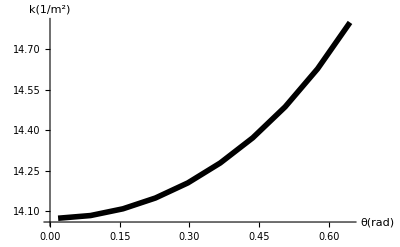

```mathematica
plotsq=ListPlot[kdatasq,PlotJoined-> True,AxesLabel-> {θ [rad],k[1/m^2]},PlotStyle->{Dashing->False,Black,Thickness[0.01]}]
```

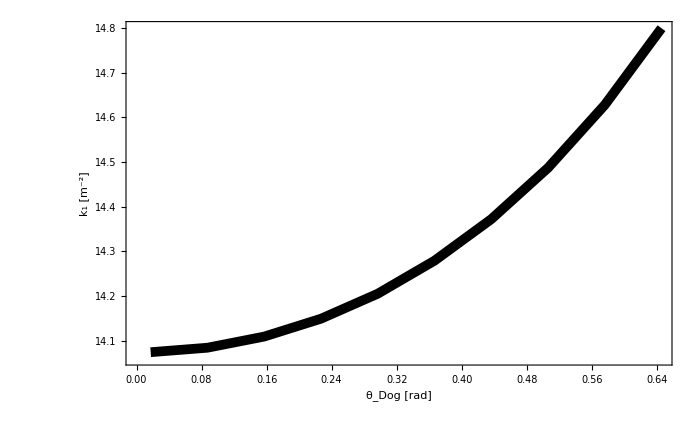

```mathematica
testplot=Show[plotsq,ImageSize->700,Frame->True,GridLines->None,Frame->True,FrameLabel-> {"θ_Dog [rad]","k_1 [m^-2]"},BaseStyle->{FontSize->25,FontFamily->"Times",PrivateFontOptions->{"FontPostScriptName"->Automatic}},ImageSize->1000]
```

```mathematica
Export["fig_7_1p2.eps", testplot]; Export["fig_7_1p2.png", testplot]
```

fig_7_1p2.png

Fit the solution to a quadratic / cubic

```mathematica
kfit=Fit[kdatasq,{1,θ,θ^2,θ^3},θ]
```

14.0712+0.0724153 θ+0.951836 θ^2+1.05328 θ^3

```mathematica
kfuncsq[θ_]:=14.071200009105485+0.07241532520496234 θ+0.9518356880411669 θ^2+1.053284651085912 θ^3
```

Check that these lie close together

```mathematica
kfuncsqvals=Table[{i,kfuncsq[i]},{i,0.01,0.6,0.01}]
```

{{0.01,14.072},{0.02,14.073},{0.03,14.0743},{0.04,14.0757},{0.05,14.0773},{0.06,14.0792},{0.07,14.0813},{0.08,14.0836},{0.09,14.0862},{0.1,14.089},{0.11,14.0921},{0.12,14.0954},{0.13,14.099},{0.14,14.1029},{0.15,14.107},{0.16,14.1115},{0.17,14.1162},{0.18,14.1212},{0.19,14.1265},{0.2,14.1322},{0.21,14.1381},{0.22,14.1444},{0.23,14.151},{0.24,14.158},{0.25,14.1653},{0.26,14.1729},{0.27,14.1809},{0.28,14.1892},{0.29,14.1979},{0.3,14.207},{0.31,14.2165},{0.32,14.2264},{0.33,14.2366},{0.34,14.2473},{0.35,14.2583},{0.36,14.2698},{0.37,14.2817},{0.38,14.294},{0.39,14.3067},{0.4,14.3199},{0.41,14.3335},{0.42,14.3476},{0.43,14.3621},{0.44,14.3771},{0.45,14.3925},{0.46,14.4084},{0.47,14.4249},{0.48,14.4417},{0.49,14.4591},{0.5,14.477},{0.51,14.4954},{0.52,14.5143},{0.53,14.5338},{0.54,14.5537},{0.55,14.5742},{0.56,14.5952},{0.57,14.6168},{0.58,14.6389},{0.59,14.6616},{0.6,14.6848}}

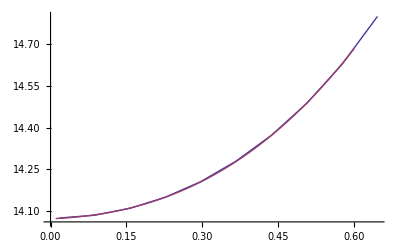

```mathematica
ListPlot[{kdatasq,kfuncsqvals},PlotJoined-> True]
```

We now have an analytic expresstion for k(θ) for the quads in the dogleg.

Now we may construct the path corrector...

### Construct the Path Corrector - Square Dipole Case

Given fixed parameters: total R_56 and dogleg angle with fixed lengths derive other parameters. Then generalise to θ_Dog variable. The central drift space DDMID expands as the angle increases.

```mathematica
Subscript[θ, Dog]:=1.0 π/180;Subscript[L, Dog]:=0.5;Subscript[ML, Dog]:=1 Subscript[θ, Dog]/Sin[Subscript[θ, Dog]];Subscript[L, NF]:=0.5+1(1-Subscript[θ, Dog]/Sin[Subscript[θ, Dog]]);Subscript[L, DogExt]:=0.05;Subscript[ML, Q]=0.2;
Subscript[ML, Dog];Subscript[θ, Dog];Subscript[ML, Q];
drift[DD,Subscript[L, Dog],"DD"];
drift[DDN,Subscript[L, NF],"DDN"];
drift[DDMID,0.4+ 2 (2 Subscript[L, Dog]+2 Subscript[L, NF]+2 Subscript[ML, Dog])(1.-Cos[Subscript[θ, Dog]]),"DDMID"];
drift[DDE,Subscript[L, DogExt],"DDE"];
sbend[BD3,Subscript[ML, Dog],0.0,Subscript[θ, Dog],"BD3",E1->0,E2->Subscript[θ, Dog]];
sbend[BD4,Subscript[ML, Dog],0.0,-Subscript[θ, Dog],"BD4",E1->-Subscript[θ, Dog],E2->0];
quad[Q1,Subscript[ML, Q],kfuncsq[Subscript[θ, Dog]],"Q1"];
```

```mathematica
DogLegsq := {DDE,BD4,DDN,Q1,DD,DD, Q1,DDN,BD3,DDE}
```

```mathematica
Last[MLCCumulativeRMatrices[MLCRMatrices[MADFlatten[DogLegsq]]]⟦All,5,6⟧]
```

-0.000101653

Now compensate for twice this using the chicane so that total R_56=0.08 (for example)

```mathematica
Subscript[M, T]=Subscript[M, 1E1].Subscript[M, D].Subscript[M, 2E2].Subscript[M, D6].Subscript[M, 2E1].Subscript[M, D].Subscript[M, 1E2];
```

```mathematica
L1:=1.1;L2:=0.2;ML1:=0.8;R56Tot=0.08;
```

```mathematica
ToExpression[StringTake[ToString[FindRoot[ReplaceAll[Subscript[M, T][[5,6]],{Subscript[L, B]-> ML1,Subscript[L, D]->L1,Subscript[L, D6]-> L2}]==(R56Tot-2 Last[MLCCumulativeRMatrices[MLCRMatrices[MADFlatten[DogLegsq]]]⟦All,5,6⟧]),{θ,20. π/180}]],{7,13}]]
```

0.15558

Now we have the angle for the chicane, so construct it.

```mathematica
Subscript[θ, Chi]:= ToExpression[StringTake[ToString[FindRoot[ReplaceAll[Subscript[M, T][[5,6]],{Subscript[L, B]-> ML1,Subscript[L, D]->L1,Subscript[L, D6]-> L2}]==(R56Tot-2 Last[MLCCumulativeRMatrices[MLCRMatrices[MADFlatten[DogLegsq]]]⟦All,5,6⟧]),{θ,20. π/180}]],{7,13}]];
drift[D1,L1,"D1"];
drift[D2,L2,"D2"];
sbend[BC1,ML1,0.0,Subscript[θ, Chi],"BC1",E1->0,E2->Subscript[θ, Chi]];
sbend[BC2,ML1,0.0,-Subscript[θ, Chi],"BC2",E1->-Subscript[θ, Chi],E1->0];
sbend[BC3,ML1,0.0,-Subscript[θ, Chi],"BC1",E1-> 0,E2->-Subscript[θ, Chi]];
sbend[BC4,ML1,0.0,Subscript[θ, Chi],"BC2",E1->Subscript[θ, Chi],E2->0];
```

```mathematica
Chicane:={BC1,D1,BC2,D2,BC3,D1,BC4}
```

```mathematica
PathCorrectorsq:={DogLegsq,DDMID,Reverse[DogLegsq],Chicane}
```

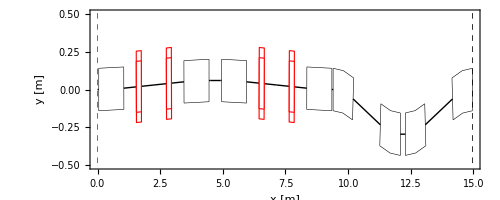

```mathematica
MADDraw[PathCorrectorsq,Frame->True,GridLines->None,TextStyle->{FontFamily->"Courier",FontSize->12},FrameLabel->{"x [m]","y [m]"}]
```

```mathematica
MADInfo[PathCorrectorsq]
```

| Name | Element | Length | Focus | VAngle | HAngle | Type | Position
1 | DDE | Drift | 0.05 | --- | --- | --- | DDE | 0.05
2 | BD4 | SectorBend | 1.00005 | 0. | --- | -0.0174533 | BD4 | 1.05005
3 | DDN | Drift | 0.499949 | --- | --- | --- | DDN | 1.55
4 | Q1 | Quadrupole | 0.2 | 14.0728 | --- | --- | Q1 | 1.75
5 | DD | Drift | 0.5 | --- | --- | --- | DD | 2.25
6 | DD | Drift | 0.5 | --- | --- | --- | DD | 2.75
7 | Q1 | Quadrupole | 0.2 | 14.0728 | --- | --- | Q1 | 2.95
8 | DDN | Drift | 0.499949 | --- | --- | --- | DDN | 3.44995
9 | BD3 | SectorBend | 1.00005 | 0. | --- | 0.0174533 | BD3 | 4.45
10 | DDE | Drift | 0.05 | --- | --- | --- | DDE | 4.5
11 | DDMID | Drift | 0.401218 | --- | --- | --- | DDMID | 4.90122
12 | DDE | Drift | 0.05 | --- | --- | --- | DDE | 4.95122
13 | BD3 | SectorBend | 1.00005 | 0. | --- | 0.0174533 | BD3 | 5.95127
14 | DDN | Drift | 0.499949 | --- | --- | --- | DDN | 6.45122
15 | Q1 | Quadrupole | 0.2 | 14.0728 | --- | --- | Q1 | 6.65122
16 | DD | Drift | 0.5 | --- | --- | --- | DD | 7.15122
17 | DD | Drift | 0.5 | --- | --- | --- | DD | 7.65122
18 | Q1 | Quadrupole | 0.2 | 14.0728 | --- | --- | Q1 | 7.85122
19 | DDN | Drift | 0.499949 | --- | --- | --- | DDN | 8.35117
20 | BD4 | SectorBend | 1.00005 | 0. | --- | -0.0174533 | BD4 | 9.35122
21 | DDE | Drift | 0.05 | --- | --- | --- | DDE | 9.40122
22 | BC1 | SectorBend | 0.8 | 0. | --- | 0.15558 | BC1 | 10.2012
23 | D1 | Drift | 1.1 | --- | --- | --- | D1 | 11.3012
24 | BC2 | SectorBend | 0.8 | 0. | --- | -0.15558 | BC2 | 12.1012
25 | D2 | Drift | 0.2 | --- | --- | --- | D2 | 12.3012
26 | BC3 | SectorBend | 0.8 | 0. | --- | -0.15558 | BC1 | 13.1012
27 | D1 | Drift | 1.1 | --- | --- | --- | D1 | 14.2012
28 | BC4 | SectorBend | 0.8 | 0. | --- | 0.15558 | BC2 | 15.0012

Total Length = 15.0012 m

```mathematica
MADPathLengthDiff[PathCorrectorsq]
```

0.0404521

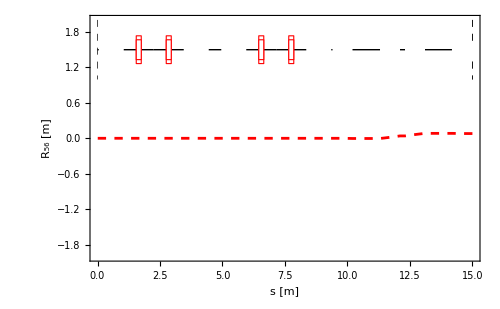

```mathematica
{MLCS=MADGetLengths[MADSplitElements[{PathCorrectorsq},#]],MLCRpositive=Rest[MLCCumulativeRMatrices[MLCRMatrices[MADSplitElements[{PathCorrectorsq},#]]]]}&[5];Show[mfsPlot[{{MLCS,(#[[5,6]]&/@MLCRpositive)}},PlotRange->{{0,Last[MLCS]},{-2,2.0}}, Frame->True,GridLines->None,TextStyle->{FontFamily->"Courier",FontSize->12},FrameLabel->{"s [m]","R_56 [m]"},DisplayFunction->Identity],MADDraw[{PathCorrectorsq},Bends->False,DisplayFunction->Identity,Offset->1.5,Labels->False,Thick->0.001],DisplayFunction->$DisplayFunction,ImageSize->500]
```

```mathematica
{MLCElems,MLCS,MLCBETX,MLCALFX,MLCGAMX,MLCBETY,MLCALFY,MLCGAMY,MLCMUX,MLCMUY,MLCDX,MLCDPX,MLCDY,MLCDPY}=MLCGenerateTwissTable[MADSplitElements[{PathCorrectorsq},10],spti,{0,0},spdi];
Last[MLCDX]
```

0.000329965

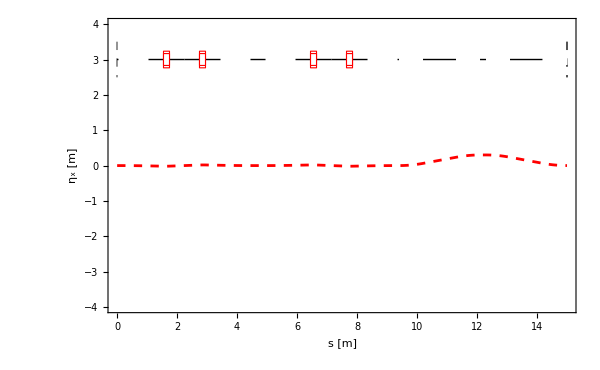

```mathematica
Show[mfsPlot[{{MLCS,MLCDX}},PlotRange->{{0,Last[MLCS]},{-4,4.0}}, Frame->True,GridLines->None,TextStyle->{FontFamily->"Courier",FontSize->12},FrameLabel->{"s [m]","η_x [m]"},DisplayFunction->Identity],MADDraw[{PathCorrectorsq},Bends->False,DisplayFunction->Identity,Offset->3,Labels->False,Thick->0.001],DisplayFunction->$DisplayFunction,ImageSize->600]
```

```mathematica
Last[MLCCumulativeRMatrices[MLCRMatrices[MADFlatten[PathCorrectorsq]]]⟦All,5,6⟧]
```

0.0799905

This all works nicely, so generalise. Putting this altogether i can make a table of θ_Chi, k_Dogand path length difference as a function of θ_Dog. Fixed parameters are L_Dog , ML_Dog, L1, L2, ML_Chi and R56Tot.

```mathematica
PathCorrectorsqData=Flatten[Reap[For[i=0,i <40, i++,
Subscript[θ, Dog]:=( Re[i] +1.)/2 π/180.;
Subscript[L, Dog]:=0.5 ;
Subscript[L, DogExt]:=0.05;
Subscript[ML, Dog]:=1 Subscript[θ, Dog]/Sin[Subscript[θ, Dog]];Subscript[ML, Q]=0.2;
Subscript[L, NF]:=0.5+1(1-Subscript[θ, Dog]/Sin[Subscript[θ, Dog]]);
drift[DD,Subscript[L, Dog],"DD"];
drift[DDN,Subscript[L, NF],"DDN"];
drift[DDE,Subscript[L, DogExt],"DDE"];
drift[DDMID,0.4+ 2 (2 Subscript[L, Dog]+2 Subscript[L, NF]+2 Subscript[ML, Dog])(1.-Cos[Subscript[θ, Dog]]),"DDMID"];
sbend[BD4,Subscript[ML, Dog],0.0,Subscript[θ, Dog],"BD4",E1->0,E2->Subscript[θ, Dog]];
sbend[BD3,Subscript[ML, Dog],0.0,-Subscript[θ, Dog],"BD3",E1->-Subscript[θ, Dog],E2->0];
sbend[BD2,Subscript[ML, Dog],0.0,Subscript[θ, Dog],"BD2",E1->0,E2->Subscript[θ, Dog]];
sbend[BD1,Subscript[ML, Dog],0.0,-Subscript[θ, Dog],"BD1",E1->-Subscript[θ, Dog],E2->0];
quad[Q1,Subscript[ML, Q],kfuncsq[Subscript[θ, Dog]],"Q1"];
DogLegsq := {DDE,BD4,DDN,Q1,DD,DD,Q1,DDN,BD3,DDE};
RDogLegsq := {DDE,BD1,DDN,Q1,DD,DD,Q1,DDN,BD2,DDE};
Subscript[M, T]=Subscript[M, 1E1].Subscript[M, D].Subscript[M, 2E2].Subscript[M, D6].Subscript[M, 2E1].Subscript[M, D].Subscript[M, 1E2];
L1:=1.1 ;
L2:=0.2;
Subscript[ML, Chi]:=0.8;
R56Tot=0.08;
Subscript[θ, Chi]:= ToExpression[StringTake[ToString[FindRoot[ReplaceAll[Subscript[M, T][[5,6]],{Subscript[L, B]-> Subscript[ML, Chi],Subscript[L, D]->L1 Cos[0.15558]/Cos[θ],Subscript[L, D6]-> L2}]==(R56Tot-2 Last[MLCCumulativeRMatrices[MLCRMatrices[MADFlatten[DogLegsq]]]⟦All,5,6⟧]),{θ,20. π/180}]],{7,11}]];
drift[D1,L1 Cos[0.15558]/Cos[Subscript[θ, Chi]],"D1"];
drift[D2,L2,"D2"];
sbend[BC4,Subscript[ML, Chi],0.0,Subscript[θ, Chi],"BC2",E1->Subscript[θ, Chi],E2->0];
sbend[BC3,Subscript[ML, Chi],0.0,-Subscript[θ, Chi],"BC1",E1->0,E2->-Subscript[θ, Chi]];
sbend[BC2,Subscript[ML, Chi],0.0,-Subscript[θ, Chi],"BC1",E1->-Subscript[θ, Chi],E2->0];
sbend[BC1,Subscript[ML, Chi],0.0,Subscript[θ, Chi],"BC2",E1->0,E2->Subscript[θ, Chi]];
Chicane:={BC1,D1,BC2,D2,BC3,D1,BC4};
PathCorrectorsq:={DogLegsq,DDMID,RDogLegsq,Chicane};
Sow[{Subscript[θ, Dog] 180/π,Subscript[θ, Chi] 180/π,kfuncsq[Subscript[θ, Dog]],MADPathLengthDiff[PathCorrectorsq],MADPathLengthDiff[PathCorrectorsq] (1.3 10^9)/(2.998 10^8)}]]][[2]],1]
```

{{0.5,8.88085,14.0719,0.0394551,0.171086},{1.,8.88085,14.0728,0.0401557,0.174124},{1.5,8.88085,14.0738,0.0413233,0.179187},{2.,8.93814,14.0749,0.0434694,0.188493},{2.5,8.93814,14.0763,0.0455705,0.197604},{3.,8.99544,14.0778,0.0486532,0.210971},{3.5,8.99544,14.0794,0.051687,0.224126},{4.,9.05273,14.0813,0.0557052,0.24155},{4.5,9.11003,14.0833,0.0601923,0.261007},{5.,9.16732,14.0855,0.065148,0.282496},{5.5,9.22462,14.0879,0.0705718,0.306015},{6.,9.28192,14.0904,0.0764631,0.331561},{6.5,9.33921,14.0932,0.0828215,0.359133},{7.,9.39651,14.0962,0.0896463,0.388726},{7.5,9.4538,14.0994,0.0969369,0.42034},{8.,9.5684,14.1027,0.105242,0.456352},{8.5,9.62569,14.1063,0.113465,0.492011},{9.,9.74028,14.1101,0.122712,0.532106},{9.5,9.79758,14.1142,0.131865,0.571797},{10.,9.91217,14.1184,0.14205,0.615961},{10.5,10.0268,14.1229,0.152706,0.662169},{11.,10.1414,14.1276,0.163833,0.710416},{11.5,10.2559,14.1326,0.175429,0.760698},{12.,10.3705,14.1378,0.187493,0.813011},{12.5,10.4851,14.1432,0.200024,0.867349},{13.,10.5997,14.1489,0.213021,0.923709},{13.5,10.7143,14.1549,0.226484,0.982084},{14.,10.8289,14.1611,0.24041,1.04247},{14.5,10.9435,14.1676,0.254798,1.10486},{15.,11.0581,14.1743,0.269647,1.16925},{15.5,11.23,14.1813,0.285606,1.23845},{16.,11.3446,14.1886,0.30138,1.30685},{16.5,11.5165,14.1961,0.318278,1.38013},{17.,11.631,14.204,0.334972,1.45251},{17.5,11.8029,14.2121,0.352804,1.52984},{18.,11.9175,14.2206,0.370411,1.60618},{18.5,12.0894,14.2293,0.389171,1.68753},{19.,12.204,14.2383,0.407685,1.76781},{19.5,12.3759,14.2476,0.427366,1.85315},{20.,12.5478,14.2573,0.44751,1.9405}}

```mathematica
TableForm[PathCorrectorsqData,TableHeadings-> {None,{"θ_Dog [°]","θ_Chi [°]","k_Dog [m^-2]","PLD [m]",PLD/λ}}]
```

θ_Dog [°] | θ_Chi [°] | k_Dog [m^-2] | PLD [m] | PLD/λ
0.5 | 8.88085 | 14.0719 | 0.0394551 | 0.171086
1. | 8.88085 | 14.0728 | 0.0401557 | 0.174124
1.5 | 8.88085 | 14.0738 | 0.0413233 | 0.179187
2. | 8.93814 | 14.0749 | 0.0434694 | 0.188493
2.5 | 8.93814 | 14.0763 | 0.0455705 | 0.197604
3. | 8.99544 | 14.0778 | 0.0486532 | 0.210971
3.5 | 8.99544 | 14.0794 | 0.051687 | 0.224126
4. | 9.05273 | 14.0813 | 0.0557052 | 0.24155
4.5 | 9.11003 | 14.0833 | 0.0601923 | 0.261007
5. | 9.16732 | 14.0855 | 0.065148 | 0.282496
5.5 | 9.22462 | 14.0879 | 0.0705718 | 0.306015
6. | 9.28192 | 14.0904 | 0.0764631 | 0.331561
6.5 | 9.33921 | 14.0932 | 0.0828215 | 0.359133
7. | 9.39651 | 14.0962 | 0.0896463 | 0.388726
7.5 | 9.4538 | 14.0994 | 0.0969369 | 0.42034
8. | 9.5684 | 14.1027 | 0.105242 | 0.456352
8.5 | 9.62569 | 14.1063 | 0.113465 | 0.492011
9. | 9.74028 | 14.1101 | 0.122712 | 0.532106
9.5 | 9.79758 | 14.1142 | 0.131865 | 0.571797
10. | 9.91217 | 14.1184 | 0.14205 | 0.615961
10.5 | 10.0268 | 14.1229 | 0.152706 | 0.662169
11. | 10.1414 | 14.1276 | 0.163833 | 0.710416
11.5 | 10.2559 | 14.1326 | 0.175429 | 0.760698
12. | 10.3705 | 14.1378 | 0.187493 | 0.813011
12.5 | 10.4851 | 14.1432 | 0.200024 | 0.867349
13. | 10.5997 | 14.1489 | 0.213021 | 0.923709
13.5 | 10.7143 | 14.1549 | 0.226484 | 0.982084
14. | 10.8289 | 14.1611 | 0.24041 | 1.04247
14.5 | 10.9435 | 14.1676 | 0.254798 | 1.10486
15. | 11.0581 | 14.1743 | 0.269647 | 1.16925
15.5 | 11.23 | 14.1813 | 0.285606 | 1.23845
16. | 11.3446 | 14.1886 | 0.30138 | 1.30685
16.5 | 11.5165 | 14.1961 | 0.318278 | 1.38013
17. | 11.631 | 14.204 | 0.334972 | 1.45251
17.5 | 11.8029 | 14.2121 | 0.352804 | 1.52984
18. | 11.9175 | 14.2206 | 0.370411 | 1.60618
18.5 | 12.0894 | 14.2293 | 0.389171 | 1.68753
19. | 12.204 | 14.2383 | 0.407685 | 1.76781
19.5 | 12.3759 | 14.2476 | 0.427366 | 1.85315
20. | 12.5478 | 14.2573 | 0.44751 | 1.9405

This table has all the design information we need, lets plot PLD against dogleg angle

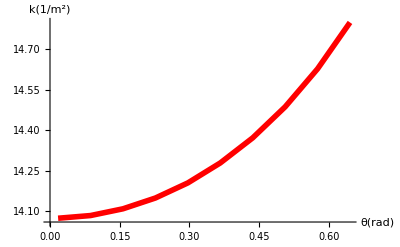

```mathematica
plotsq=ListPlot[kdatasq,PlotJoined-> True,AxesLabel-> {θ [rad],k[1/m^2]},PlotStyle->{Dashing->False,Red,Thickness[0.01]}]
```

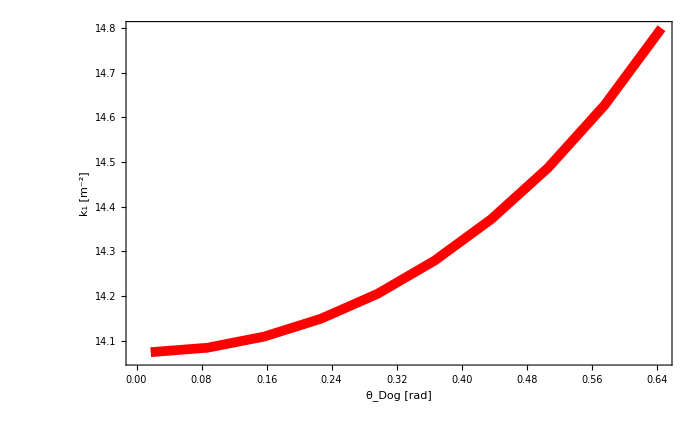

```mathematica
testplot=Show[plotsq,ImageSize->700,Frame->True,GridLines->None,Frame->True,FrameLabel-> {"θ_Dog [rad]","k_1 [m^-2]"},BaseStyle->{FontSize->25,FontFamily->"Helvetica"},ImageSize->1000]
```

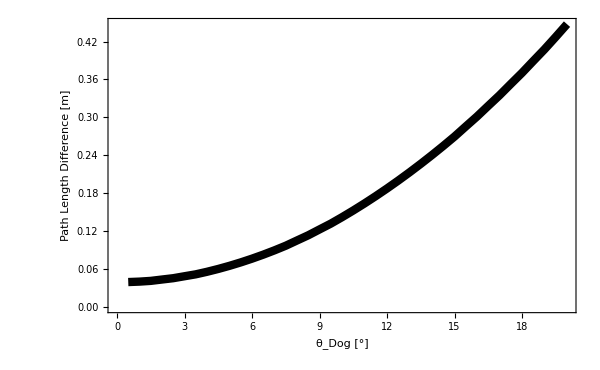

```mathematica
ListPlot[Table[{PathCorrectorsqData[[i,1]],PathCorrectorsqData[[i,4]]},{i,Length[PathCorrectorsqData]}],PlotJoined-> True,PlotStyle->{Dashing->False,Black,Thickness[0.01]},Frame->True,GridLines->None,TextStyle->{FontFamily->"Times",FontSize->25,PrivateFontOptions->{"FontPostScriptName"->Automatic}},FrameLabel-> {"θ_Dog [°]","Path Length Difference [m]"},ImageSize-> 600]
```

This is all done in total line length... [m]

```mathematica
MADLineLength[PathCorrectorsq]
```

15.1714

Let me plot this as a fraction of the wavelength at 1.3GHz

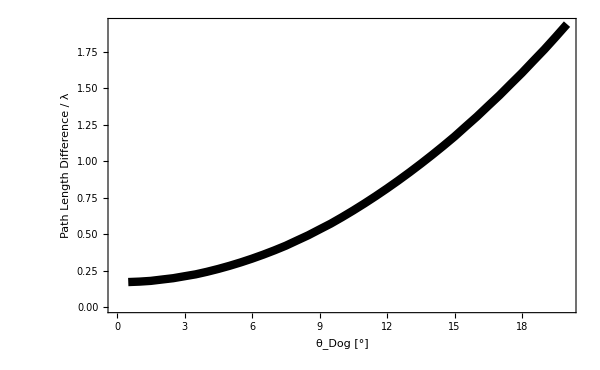

```mathematica
plot22=ListPlot[Table[{PathCorrectorsqData[[i,1]],PathCorrectorsqData[[i,4]] (1.3 10^9)/(2.998 10^8)},{i,Length[PathCorrectorsqData]}],PlotJoined-> True,Frame->True,PlotStyle->{Dashing->False,Black,Thickness[0.01]},GridLines->None,TextStyle->{FontFamily->"Helvetica",FontSize->25},FrameLabel-> {"θ_Dog [°]","Path Length Difference / λ"},ImageSize-> 600]
```

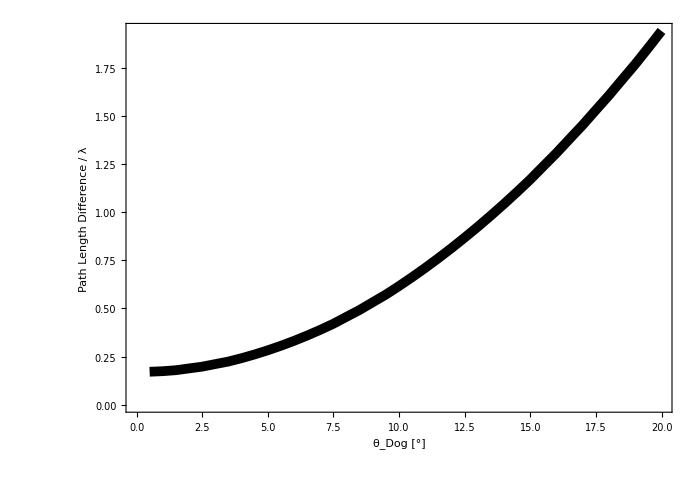

```mathematica
testplot=Show[plot22,ImageSize->700,Frame->True,GridLines->None,TextStyle->{FontFamily->"Times",PrivateFontOptions->{"FontPostScriptName"->Automatic},FontSize->25},FrameLabel-> {"θ_Dog [°]","Path Length Difference / λ"},AspectRatio->0.7]
```

```mathematica
Export["fig_16_1p2.eps", testplot]; Export["fig_16_1p2.png", testplot]
```

fig_16_1p2.png

### Max and Min Path Correction - Square Dipole Case

The parameters for the nominal minimum path correction of θ_Dog=0.5[\Degree], introducing 0.941 λ path diff are

```mathematica
Subscript[θ, Dog]:=0.5 π/180.;
Subscript[L, Dog]:=0.5 ;
Subscript[L, DogExt]:=0.05;
Subscript[ML, Dog]:=1 Subscript[θ, Dog]/Sin[Subscript[θ, Dog]];Subscript[ML, Q]:=0.2;
Subscript[L, NF]:=0.5+1(1-Subscript[θ, Dog]/Sin[Subscript[θ, Dog]]);
drift[DD,Subscript[L, Dog],"DD"];
drift[DDE,Subscript[L, DogExt],"DDE"];
drift[DDN,Subscript[L, NF],"DDN"];
drift[DDMID,0.4+ 2 (2 Subscript[L, Dog]+2 Subscript[L, NF]+2 Subscript[ML, Dog])(1.-Cos[Subscript[θ, Dog]]),"DDMID"];
sbend[BD4,Subscript[ML, Dog],0.0,Subscript[θ, Dog],"BD4",E1->0,E2->Subscript[θ, Dog]];
sbend[BD3,Subscript[ML, Dog],0.0,-Subscript[θ, Dog],"BD3",E1->-Subscript[θ, Dog],E2->0];
sbend[BD2,Subscript[ML, Dog],0.0,Subscript[θ, Dog],"BD2",E1->Subscript[θ, Dog],E2->0];
sbend[BD1,Subscript[ML, Dog],0.0,-Subscript[θ, Dog],"BD1",E1->0,E2->-Subscript[θ, Dog]];
quad[Q1,Subscript[ML, Q],kfuncsq[Subscript[θ, Dog]],"Q1"];
DogLegsq := {DDE,BD4,DDN,Q1,DD,DD,Q1,DDN,BD3,DDE};
RDogLegsq := {DDE,BD1,DDN,Q1,DD,DD,Q1,DDN,BD2,DDE};
Subscript[M, T]=Subscript[M, 1E1].Subscript[M, D].Subscript[M, 2E2].Subscript[M, D6].Subscript[M, 2E1].Subscript[M, D].Subscript[M, 1E2];
L1:=1.1 ;
L2:=0.2;
Subscript[ML, Chi]:=0.8;
R56Tot=0.08;
Subscript[θ, Chi]:= ToExpression[StringTake[ToString[FindRoot[ReplaceAll[Subscript[M, T][[5,6]],{Subscript[L, B]-> Subscript[ML, Chi],Subscript[L, D]->L1 Cos[0.15558]/Cos[θ],Subscript[L, D6]-> L2}]==(R56Tot-2 Last[MLCCumulativeRMatrices[MLCRMatrices[MADFlatten[DogLegsq]]]⟦All,5,6⟧]),{θ,20. π/180}]],{7,13}]];
drift[D1,L1 Cos[0.15558]/Cos[Subscript[θ, Chi]],"D1"];
drift[D2,L2,"D2"];
sbend[BC4,Subscript[ML, Chi],0.0,Subscript[θ, Chi],"BC2",E1->Subscript[θ, Chi],E2->0];
sbend[BC3,Subscript[ML, Chi],0.0,-Subscript[θ, Chi],"BC1",E1->0,E2->-Subscript[θ, Chi]];
sbend[BC2,Subscript[ML, Chi],0.0,-Subscript[θ, Chi],"BC1",E1->-Subscript[θ, Chi],E2->0];
sbend[BC1,Subscript[ML, Chi],0.0,Subscript[θ, Chi],"BC2",E1->0,E2->Subscript[θ, Chi]];
Chicane:={BC1,D1,BC2,D2,BC3,D1,BC4};
PathCorrectorMinsq={DogLegsq,DDMID,RDogLegsq,Chicane};
```

```mathematica
MADInfo[PathCorrectorMinsq]
```

| Name | Element | Length | Focus | VAngle | HAngle | Type | Position
1 | DDE | Drift | 0.05 | --- | --- | --- | DDE | 0.05
2 | BD4 | SectorBend | 1.00001 | 0. | --- | 0.00872665 | BD4 | 1.05001
3 | DDN | Drift | 0.499987 | --- | --- | --- | DDN | 1.55
4 | Q1 | Quadrupole | 0.2 | 14.0719 | --- | --- | Q1 | 1.75
5 | DD | Drift | 0.5 | --- | --- | --- | DD | 2.25
6 | DD | Drift | 0.5 | --- | --- | --- | DD | 2.75
7 | Q1 | Quadrupole | 0.2 | 14.0719 | --- | --- | Q1 | 2.95
8 | DDN | Drift | 0.499987 | --- | --- | --- | DDN | 3.44999
9 | BD3 | SectorBend | 1.00001 | 0. | --- | -0.00872665 | BD3 | 4.45
10 | DDE | Drift | 0.05 | --- | --- | --- | DDE | 4.5
11 | DDMID | Drift | 0.400305 | --- | --- | --- | DDMID | 4.9003
12 | DDE | Drift | 0.05 | --- | --- | --- | DDE | 4.9503
13 | BD1 | SectorBend | 1.00001 | 0. | --- | -0.00872665 | BD1 | 5.95032
14 | DDN | Drift | 0.499987 | --- | --- | --- | DDN | 6.4503
15 | Q1 | Quadrupole | 0.2 | 14.0719 | --- | --- | Q1 | 6.6503
16 | DD | Drift | 0.5 | --- | --- | --- | DD | 7.1503
17 | DD | Drift | 0.5 | --- | --- | --- | DD | 7.6503
18 | Q1 | Quadrupole | 0.2 | 14.0719 | --- | --- | Q1 | 7.8503
19 | DDN | Drift | 0.499987 | --- | --- | --- | DDN | 8.35029
20 | BD2 | SectorBend | 1.00001 | 0. | --- | 0.00872665 | BD2 | 9.3503
21 | DDE | Drift | 0.05 | --- | --- | --- | DDE | 9.4003
22 | BC1 | SectorBend | 0.8 | 0. | --- | 0.15544 | BC2 | 10.2003
23 | D1 | Drift | 1.09998 | --- | --- | --- | D1 | 11.3003
24 | BC2 | SectorBend | 0.8 | 0. | --- | -0.15544 | BC1 | 12.1003
25 | D2 | Drift | 0.2 | --- | --- | --- | D2 | 12.3003
26 | BC3 | SectorBend | 0.8 | 0. | --- | -0.15544 | BC1 | 13.1003
27 | D1 | Drift | 1.09998 | --- | --- | --- | D1 | 14.2003
28 | BC4 | SectorBend | 0.8 | 0. | --- | 0.15544 | BC2 | 15.0003

Total Length = 15.0003 m

This is unsuitable for formatting to TEX as input for the report

```mathematica
MADInfo2[data2_,Opts___]:=Block[{a,data},
notable=NoTable/.{Opts}/.Options[MADInfo];
expand=LineExpand/.{Opts}/.Options[MADInfo];
data=If[expand===True,ExpandLattice[data2],LinesLattice[data2]];
a=Partition[Flatten[MapThread[List,{data,Drop[FoldList[Plus,0,data⟦All,3⟧],1]}]],8];
If[notable===False,Return[TableForm[a,TableAlignments->Center, TableHeadings->{Automatic,{"Name","Element","Length","Focus","VAngle","HAngle","Type","Position"}}]];
Print["Total Length = "<>ToString[Fold[Plus,0,data⟦All,3⟧]]<>" m"],a]
]
```

Export["test.tex", MADInfo2[PathCorrectorMinsq]]

test.tex

```mathematica
$ExportFormats
```

{3DS,ACO,AIFF,AU,AVI,Base64,Binary,Bit,BMP,Byte,BYU,BZIP2,C,CDF,Character16,Character8,Complex128,Complex256,Complex64,CSV,DICOM,DIF,DIMACS,DOT,DXF,EMF,EPS,ExpressionML,FASTA,FITS,FLAC,FLV,GIF,Graph6,Graphlet,GraphML,GXL,GZIP,HarwellBoeing,HDF,HDF5,HTML,Integer128,Integer16,Integer24,Integer32,Integer64,Integer8,JPEG,JPEG2000,JSON,JVX,KML,LEDA,List,LWO,MAT,MathML,Maya,MGF,MIDI,MOL,MOL2,MTX,MX,NASACDF,NB,NetCDF,NEXUS,NOFF,OBJ,OFF,Package,Pajek,PBM,PCX,PDB,PDF,PGM,PLY,PNG,PNM,POV,PPM,PXR,QuickTime,RawBitmap,Real128,Real32,Real64,RIB,RTF,SCT,SDF,SND,Sparse6,STL,String,SurferGrid,SVG,SWF,Table,TAR,TerminatedString,TeX,Text,TGA,TGF,TIFF,TSV,UnsignedInteger128,UnsignedInteger16,UnsignedInteger24,UnsignedInteger32,UnsignedInteger64,UnsignedInteger8,UUE,VideoFrames,VRML,VTK,WAV,Wave64,WDX,WMF,X3D,XBM,XHTML,XHTMLMathML,XLS,XLSX,XML,XYZ,ZIP,ZPR}

```mathematica
MADFootPrint[PathCorrectorMinsq]
```

{14.9606,0.294394}

```mathematica
MADPathLength[PathCorrectorMinsq]
```

15.0132

```mathematica
MADLineLength[PathCorrectorMinsq]
```

14.9735

This looks like

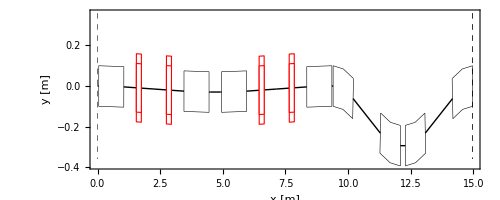

```mathematica
plot2=MADDraw[PathCorrectorMinsq,WidthScale->1,Thickness->0.001,Frame->True,GridLines->None,TextStyle->{FontFamily->"Courier",FontSize->12},FrameLabel->{"x [m]","y [m]"}]
```

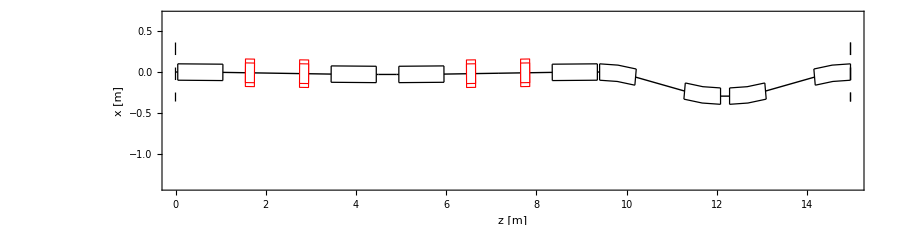

```mathematica
testplot=Show[plot2,ImageSize->900,Frame->True,GridLines->None,PlotRange->{Automatic,{-1.4,0.7}},TextStyle->{FontFamily-> "Times",PrivateFontOptions->{"FontPostScriptName"->Automatic},FontSize->25},FrameLabel->{"z [m]","x [m]"},AspectRatio->0.25]
```

```mathematica
Export["fig_9_1p2.eps", testplot]; Export["fig_9_1p2.png", testplot]
```

fig_9_1p2.png

And for maximum where we introduce 2λ path diff

```mathematica
Subscript[θ, Dog]:=20 π/180.;
Subscript[L, Dog]:=0.5 ;
Subscript[L, DogExt]:=0.05;
Subscript[ML, Dog]:=1 Subscript[θ, Dog]/Sin[Subscript[θ, Dog]];Subscript[ML, Q]:=0.2;
Subscript[L, NF]:=0.5+1(1-Subscript[θ, Dog]/Sin[Subscript[θ, Dog]]);
drift[DD,Subscript[L, Dog],"DD"];
drift[DDN,Subscript[L, NF],"DDN"];
drift[DDE,Subscript[L, DogExt],"DDE"];
drift[DDMID,0.4+ 2 (2 Subscript[L, Dog]+2 Subscript[L, NF]+2 Subscript[ML, Dog]+2 Subscript[ML, Q])(1.-Cos[Subscript[θ, Dog]]),"DDMID"];
sbend[BD4,Subscript[ML, Dog],0.0,Subscript[θ, Dog],"BD4",E1->0,E2->Subscript[θ, Dog]];
sbend[BD3,Subscript[ML, Dog],0.0,-Subscript[θ, Dog],"BD3",E1->-Subscript[θ, Dog],E2->0];
sbend[BD2,Subscript[ML, Dog],0.0,Subscript[θ, Dog],"BD2",E1->Subscript[θ, Dog],E2->0];
sbend[BD1,Subscript[ML, Dog],0.0,-Subscript[θ, Dog],"BD1",E1->0,E2->-Subscript[θ, Dog]];
quad[Q1,Subscript[ML, Q],kfuncsq[Subscript[θ, Dog]],"Q1"];
DogLegsq := {DDE,BD4,DDN,Q1,DD,DD,Q1,DDN,BD3,DDE};
RDogLegsq := {DDE,BD1,DDN,Q1,DD,DD,Q1,DDN,BD2,DDE};
Subscript[M, T]=Subscript[M, 1E1].Subscript[M, D].Subscript[M, 2E2].Subscript[M, D6].Subscript[M, 2E1].Subscript[M, D].Subscript[M, 1E2];
L1:=1.1 ;
L2:=0.2;
Subscript[ML, Chi]:=0.8;
R56Tot=0.08;
Subscript[θ, Chi]:= ToExpression[StringTake[ToString[FindRoot[ReplaceAll[Subscript[M, T][[5,6]],{Subscript[L, B]-> Subscript[ML, Chi],Subscript[L, D]->L1 Cos[0.15558]/Cos[θ],Subscript[L, D6]-> L2}]==(R56Tot-2 Last[MLCCumulativeRMatrices[MLCRMatrices[MADFlatten[DogLegsq]]]⟦All,5,6⟧]),{θ,20. π/180}]],{7,12}]];
drift[D1,L1 Cos[0.15558]/Cos[Subscript[θ, Chi]],"D1"];
drift[D2,L2,"D2"];
sbend[BC4,Subscript[ML, Chi],0.0,Subscript[θ, Chi],"BC2",E1->Subscript[θ, Chi],E2->0];
sbend[BC3,Subscript[ML, Chi],0.0,-Subscript[θ, Chi],"BC1",E1->0,E2->-Subscript[θ, Chi]];
sbend[BC2,Subscript[ML, Chi],0.0,-Subscript[θ, Chi],"BC1",E1->-Subscript[θ, Chi],E2->0];
sbend[BC1,Subscript[ML, Chi],0.0,Subscript[θ, Chi],"BC2",E1->0,E2->Subscript[θ, Chi]];
Chicane:={BC1,D1,BC2,D2,BC3,D1,BC4};
PathCorrectorMaxsq={DogLegsq,DDMID,RDogLegsq,Chicane};
```

Remember Reverse[DogLeg] does NOT work as we need to take into account the precise edge structure

```mathematica
Export["max_info.tex", ToBoxes[MADInfo[PathCorrectorMaxsq]], "TeX"]
```

| Name | Element | Length | Focus | VAngle | HAngle | Type | Position
1 | DDE | Drift | 0.05 | --- | --- | --- | DDE | 0.05
2 | BD4 | SectorBend | 1.0206 | 0. | --- | 0.349066 | BD4 | 1.0706
3 | DDN | Drift | 0.4794 | --- | --- | --- | DDN | 1.55
4 | Q1 | Quadrupole | 0.2 | 14.2573 | --- | --- | Q1 | 1.75
5 | DD | Drift | 0.5 | --- | --- | --- | DD | 2.25
6 | DD | Drift | 0.5 | --- | --- | --- | DD | 2.75
7 | Q1 | Quadrupole | 0.2 | 14.2573 | --- | --- | Q1 | 2.95
8 | DDN | Drift | 0.4794 | --- | --- | --- | DDN | 3.4294
9 | BD3 | SectorBend | 1.0206 | 0. | --- | -0.349066 | BD3 | 4.45
10 | DDE | Drift | 0.05 | --- | --- | --- | DDE | 4.5
11 | DDMID | Drift | 0.930705 | --- | --- | --- | DDMID | 5.4307
12 | DDE | Drift | 0.05 | --- | --- | --- | DDE | 5.4807
13 | BD1 | SectorBend | 1.0206 | 0. | --- | -0.349066 | BD1 | 6.50131
14 | DDN | Drift | 0.4794 | --- | --- | --- | DDN | 6.9807
15 | Q1 | Quadrupole | 0.2 | 14.2573 | --- | --- | Q1 | 7.1807
16 | DD | Drift | 0.5 | --- | --- | --- | DD | 7.6807
17 | DD | Drift | 0.5 | --- | --- | --- | DD | 8.1807
18 | Q1 | Quadrupole | 0.2 | 14.2573 | --- | --- | Q1 | 8.3807
19 | DDN | Drift | 0.4794 | --- | --- | --- | DDN | 8.8601
20 | BD2 | SectorBend | 1.0206 | 0. | --- | 0.349066 | BD2 | 9.8807
21 | DDE | Drift | 0.05 | --- | --- | --- | DDE | 9.9307
22 | BC1 | SectorBend | 0.8 | 0. | --- | 0.219 | BC2 | 10.7307
23 | D1 | Drift | 1.11331 | --- | --- | --- | D1 | 11.844
24 | BC2 | SectorBend | 0.8 | 0. | --- | -0.219 | BC1 | 12.644
25 | D2 | Drift | 0.2 | --- | --- | --- | D2 | 12.844
26 | BC3 | SectorBend | 0.8 | 0. | --- | -0.219 | BC1 | 13.644
27 | D1 | Drift | 1.11331 | --- | --- | --- | D1 | 14.7573
28 | BC4 | SectorBend | 0.8 | 0. | --- | 0.219 | BC2 | 15.5573

Total Length = 15.5573 m

max_info.tex

```mathematica
MADFootPrint[PathCorrectorMaxsq]
```

{15.1117,1.15941}

```mathematica
MADPathLength[PathCorrectorMaxsq]
```

15.6671

```mathematica
MADLineLength[PathCorrectorMaxsq]
```

15.2196

```mathematica
MADFootPrint[PathCorrectorMinsq]
```

{14.9606,0.294394}

```mathematica
MADPathLength[PathCorrectorMinsq]
```

15.0132

```mathematica
MADLineLength[PathCorrectorMinsq]
```

14.9735

!!! Line Length is no longer equal - down to lengthened dipoles. !!!!!!

This looks like

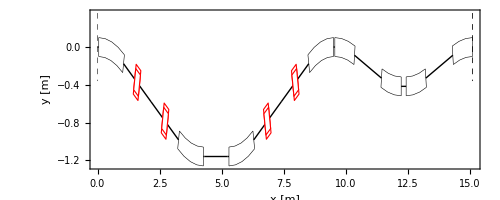

```mathematica
plot4=MADDraw[PathCorrectorMaxsq,WidthScale->1,Thickness->0.001,PlotStyle->{Black,AbsolutePointSize[4]},Frame->True,GridLines->None,TextStyle->{FontFamily->"Courier",FontSize->12},FrameLabel->{"x [m]","y [m]"}]
```

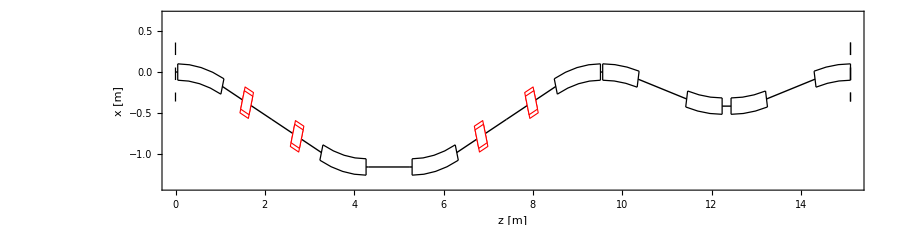

```mathematica
testplot=Show[plot4,ImageSize->900,Frame->True,GridLines->None,PlotRange->{Automatic,{-1.4,0.7}},TextStyle->{FontFamily-> "Times",PrivateFontOptions->{"FontPostScriptName"->Automatic},FontSize->25},FrameLabel->{"z [m]","x [m]"},AspectRatio->0.25]
```

```mathematica
Export["fig_10_1p2.eps", testplot]; Export["fig_10_1p2.png", testplot]
```

fig_10_1p2.png

```mathematica
spti:={MLCBetaGamma[10,0],MLCBetaGamma[10,0]};
```

```mathematica
spdi:={0,0,0,0,0,1};
```

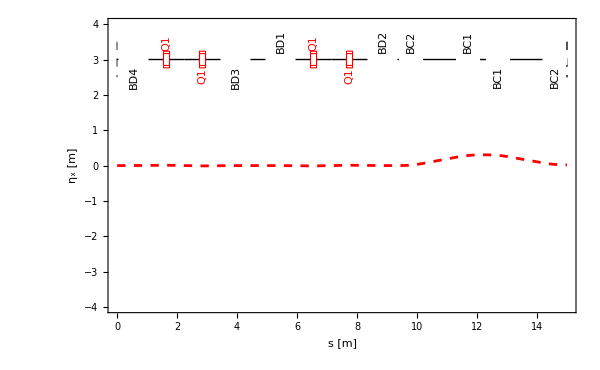

0.0204797

```mathematica
{MLCElems,MLCS,MLCBETX,MLCALFX,MLCGAMX,MLCBETY,MLCALFY,MLCGAMY,MLCMUX,MLCMUY,MLCDX,MLCDPX,MLCDY,MLCDPY}=MLCGenerateTwissTable[MADSplitElements[{PathCorrectorMinsq},10],spti,{0,0},spdi];plot5=Show[mfsPlot[{{MLCS,MLCDX}},PlotRange->{{0,Last[MLCS]},{-4,4.0}}, Frame->True,GridLines->None,TextStyle->{FontFamily->"Courier",FontSize->12},FrameLabel->{"s [m]","η_x [m]"},DisplayFunction->Identity],MADDraw[{PathCorrectorMinsq},Bends->False,DisplayFunction->Identity,Offset->3,Labels->True,Thick->0.001],DisplayFunction->$DisplayFunction,ImageSize->600]
Last[MLCDX]
```

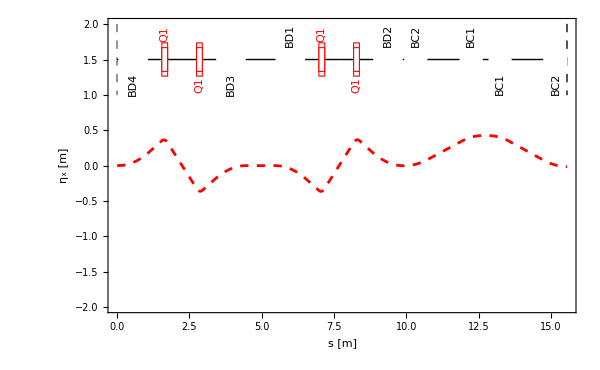

```mathematica
{MLCElems,MLCS,MLCBETX,MLCALFX,MLCGAMX,MLCBETY,MLCALFY,MLCGAMY,MLCMUX,MLCMUY,MLCDX,MLCDPX,MLCDY,MLCDPY}=MLCGenerateTwissTable[MADSplitElements[{PathCorrectorMaxsq},10],spti,{0,0},spdi];plot5=Show[mfsPlot[{{MLCS,MLCDX}},PlotRange->{{0,Last[MLCS]},{-2,2.0}}, Frame->True,GridLines->None,TextStyle->{FontFamily->"Courier",FontSize->12},FrameLabel->{"s [m]","η_x [m]"},DisplayFunction->Identity],MADDraw[{PathCorrectorMaxsq},Bends->False,DisplayFunction->Identity,Offset->1.5,Labels->True,Thick->0.001],DisplayFunction->$DisplayFunction,ImageSize->600]
Last[MLCDX];
```

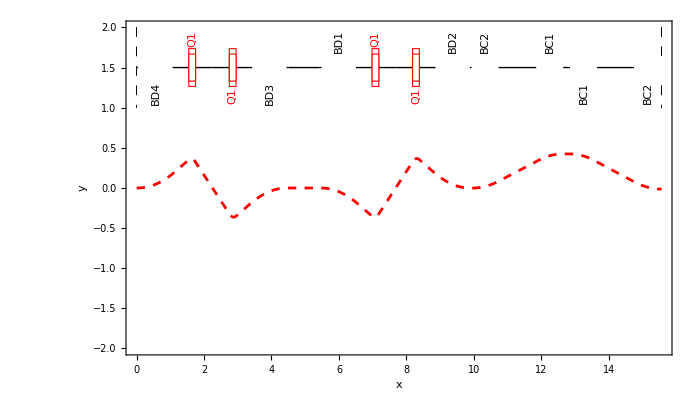

```mathematica
testplot=Show[plot5,ImageSize->700,Frame->True,GridLines->None,TextStyle->{FontFamily-> "Courier",PrivateFontOptions->{"FontPostScriptName"->Automatic},FontSize->12},FrameLabel->{"x","y"},AspectRatio->0.6]
```

Export["max_disp.eps", testplot]

max_disp.eps

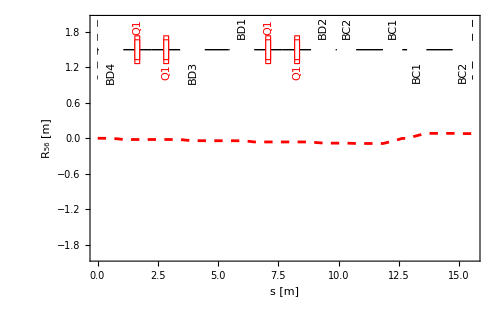

```mathematica
{MLCS=MADGetLengths[MADSplitElements[{PathCorrectorMaxsq},#]],MLCRpositive=Rest[MLCCumulativeRMatrices[MLCRMatrices[MADSplitElements[{PathCorrectorMaxsq},#]]]]}&[5];Show[mfsPlot[{{MLCS,(#[[5,6]]&/@MLCRpositive)}},PlotRange->{{0,Last[MLCS]},{-2,2.0}}, Frame->True,GridLines->None,TextStyle->{FontFamily->"Courier",FontSize->12},FrameLabel->{"s [m]","R_56 [m]"},DisplayFunction->Identity],MADDraw[{PathCorrectorMaxsq},Bends->False,DisplayFunction->Identity,Offset->1.5,Labels->True,Thick->0.001],DisplayFunction->$DisplayFunction,ImageSize->500]
```

### Beta function Matched Path Corrector - Square Dipole Case - Max Position

We need twiss parameters to calculate synchrotron H function. Here is dispersion and derivative

```mathematica
spti:={MLCBetaGamma[10,0],MLCBetaGamma[10,0]};
```

```mathematica
spdi:={0,0,0,0,0,1};
```

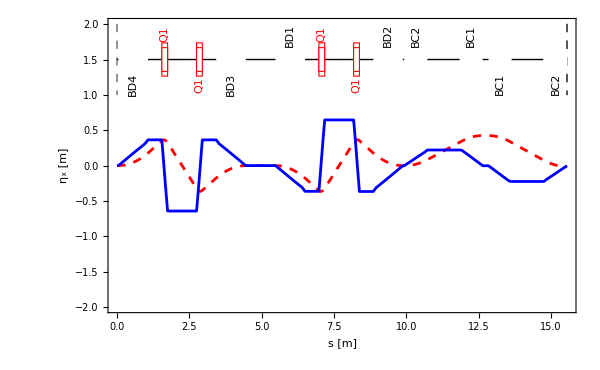

-0.0151907

```mathematica
{MLCElems,MLCS,MLCBETX,MLCALFX,MLCGAMX,MLCBETY,MLCALFY,MLCGAMY,MLCMUX,MLCMUY,MLCDX,MLCDPX,MLCDY,MLCDPY}=MLCGenerateTwissTable[MADSplitElements[{PathCorrectorMaxsq},10],spti,{0,0},spdi];plot5=Show[mfsPlot[{{MLCS,MLCDX},{MLCS,MLCDPX}},PlotRange->{{0,Last[MLCS]},{-2,2.0}}, Frame->True,GridLines->None,TextStyle->{FontFamily->"Courier",FontSize->12},FrameLabel->{"s [m]","η_x [m]"},DisplayFunction->Identity],MADDraw[{PathCorrectorMaxsq},Bends->False,DisplayFunction->Identity,Offset->1.5,Labels->True,Thick->0.001],DisplayFunction->$DisplayFunction,ImageSize->600]
Last[MLCDX]
```

in y !?!?! Check that this is zero - rectify mistake in MLCGenerateTwissTable.

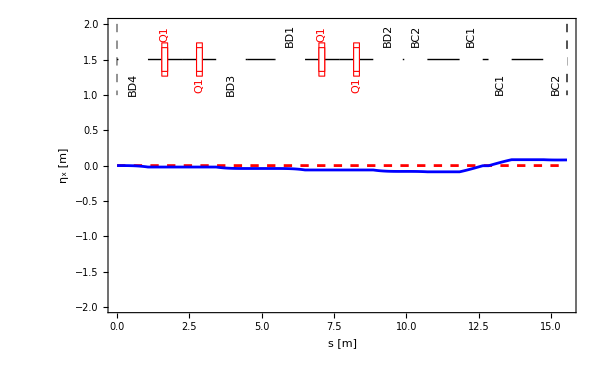

-0.0151907

```mathematica
{MLCElems,MLCS,MLCBETX,MLCALFX,MLCGAMX,MLCBETY,MLCALFY,MLCGAMY,MLCMUX,MLCMUY,MLCDX,MLCDPX,MLCDY,MLCDPY}=MLCGenerateTwissTable[MADSplitElements[{PathCorrectorMaxsq},20],spti,{0,0},spdi];plot5=Show[mfsPlot[{{MLCS,MLCDY},{MLCS,MLCDPY}},PlotRange->{{0,Last[MLCS]},{-2,2.0}}, Frame->True,GridLines->None,TextStyle->{FontFamily->"Courier",FontSize->12},FrameLabel->{"s [m]","η_x [m]"},DisplayFunction->Identity],MADDraw[{PathCorrectorMaxsq},Bends->False,DisplayFunction->Identity,Offset->1.5,Labels->True,Thick->0.001],DisplayFunction->$DisplayFunction,ImageSize->600]
Last[MLCDX]
```

```mathematica
MLCPropagateDispersion[spdi,MLCRMatrices[{PathCorrectorMaxsq}]];
```

```mathematica
Transpose[MLCPropagateDispersion[spdi,MLCRMatrices[{PathCorrectorMaxsq}]]]⟦4⟧
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
MLCGenerateTwissTable[PathCorrectorMaxsq,spti,{0,0},spdi]⟦14⟧
```

{0.,-0.0206003,-0.0206003,-0.0206003,-0.0206003,-0.0206003,-0.0206003,-0.0206003,-0.0412831,-0.0412831,-0.0412831,-0.0412831,-0.0621861,-0.0621861,-0.0621861,-0.0621861,-0.0621861,-0.0621861,-0.0621861,-0.0825665,-0.0825665,-0.0883253,-0.0883253,-0.00232724,-0.00232724,0.0831719,0.0831719,0.0798929}

Here are Twiss α,β and γ

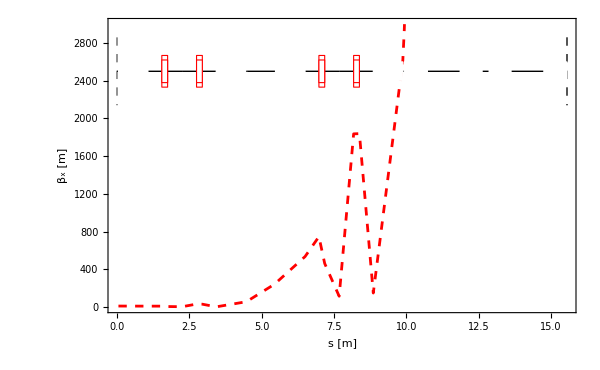

```mathematica
Show[mfsPlot[{{MLCS,MLCBETX}},PlotRange->{{0,Last[MLCS]},{0,3000.0}}, Frame->True,GridLines->None,TextStyle->{FontFamily->"Courier",FontSize->12},FrameLabel->{"s [m]","β_x [m]"},DisplayFunction-> Identity],MADDraw[{PathCorrectorMaxsq},Bends->False,DisplayFunction->Identity,Offset->2500,Labels->False,Thick->0.001,WidthScale->1000],DisplayFunction->$DisplayFunction,ImageSize->600]
```

Used MAD to match this, obtained these values

```mathematica
spti:={MLCBetaGamma[3.63801,10.87833],MLCBetaGamma[3,10]};
```

```mathematica
{MLCElems,MLCS,MLCBETX,MLCALFX,MLCGAMX,MLCBETY,MLCALFY,MLCGAMY,MLCMUX,MLCMUY,MLCDX,MLCDPX,MLCDY,MLCDPY}=MLCGenerateTwissTable[MADSplitElements[{PathCorrectorMaxsq},10],spti,{0,0},spdi];
```

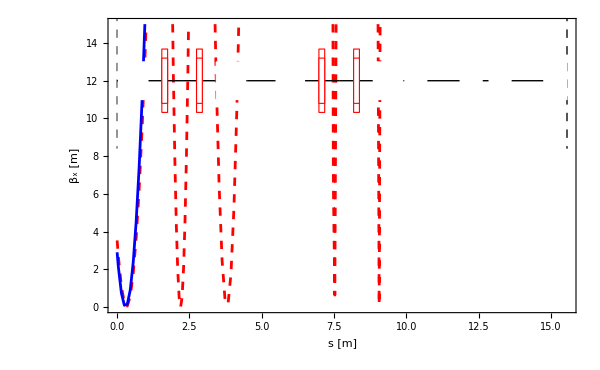

```mathematica
Show[mfsPlot[{{MLCS,MLCBETX},{MLCS,MLCBETY}},PlotRange->{{0,Last[MLCS]},{0,15.0}}, Frame->True,GridLines->None,TextStyle->{FontFamily->"Courier",FontSize->12},FrameLabel->{"s [m]","β_x [m]"},DisplayFunction-> Identity],MADDraw[{PathCorrectorMaxsq},Bends->False,DisplayFunction->Identity,Offset->12,Labels->False,Thick->0.001,WidthScale->10],DisplayFunction->$DisplayFunction,ImageSize->600]
```

Below uses MAD matching values

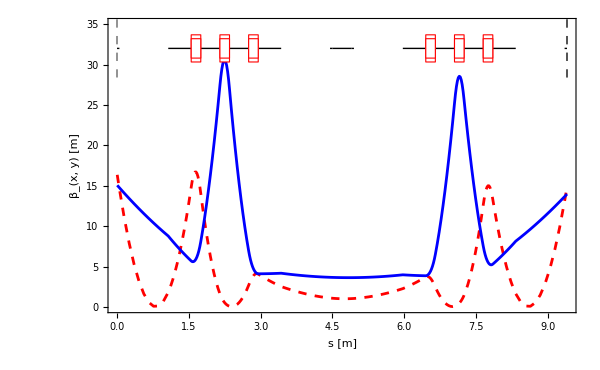

14.2573

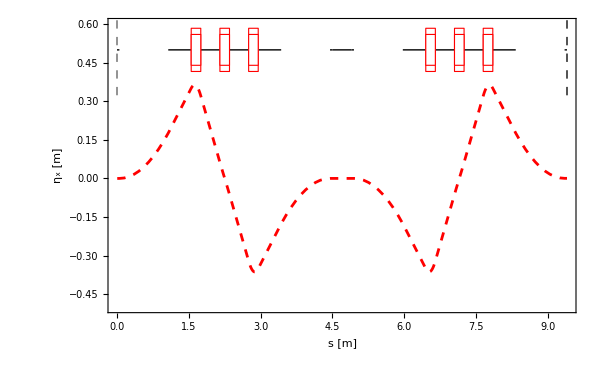
Null -Graphics-

```mathematica
Subscript[θ, Dog]:=20. π/180.;
Subscript[L, DogExt]:=0.05;
Subscript[L, DD]:=0.5;
Subscript[L, NF]:=0.5+1(1-Subscript[θ, Dog]/Sin[Subscript[θ, Dog]]);
Subscript[ML, Dog]:=1 Subscript[θ, Dog]/Sin[Subscript[θ, Dog]];
Subscript[ML, Q1]:=0.2;
Subscript[ML, Q2]:=0.2;
Subscript[L, DDM]:=Subscript[L, DD]-Subscript[ML, Q2]/2;
drift[DDN,Subscript[L, NF],"DDN"];
drift[DD,Subscript[L, DD],"DD"];
drift[DDM,Subscript[L, DDM],"DDM"];
drift[DDE,Subscript[L, DogExt],"DDE"];
drift[DDMID,N[0.4+ 2(2 Subscript[L, NF]+2 Subscript[ML, Dog]+2 Subscript[L, DDM]+2 Subscript[ML, Q1]+Subscript[ML, Q2])(1.-Cos[Subscript[θ, Dog]])],"DDMID"];
drift[DDMIDH,N[0.4+ 2(2 Subscript[L, NF]+2 Subscript[ML, Dog]+2 Subscript[L, DDM]+2 Subscript[ML, Q1]+Subscript[ML, Q2])(1.-Cos[Subscript[θ, Dog]])-Subscript[ML, Q2]/2],"DDMIDH"];
sbend[BD4,Subscript[ML, Dog],0.0,Subscript[θ, Dog],"BD4",E1->0,E2->Subscript[θ, Dog]];
sbend[BD3,Subscript[ML, Dog],0.0,-Subscript[θ, Dog],"BD3",E1->-Subscript[θ, Dog],E2->0];
sbend[BD2,Subscript[ML, Dog],0.0,Subscript[θ, Dog],"BD2",E1->Subscript[θ, Dog],E2->0];
sbend[BD1,Subscript[ML, Dog],0.0,-Subscript[θ, Dog],"BD1",E1->0,E2->-Subscript[θ, Dog]];
quad[Q1,Subscript[ML, Q1],14.319867595222,"Q1"];
quad[Q2,Subscript[ML, Q2],-11.414757884601,"Q2"];
DogLegsq := {DDE,BD4,DDN,Q1,DDM,Q2,DDM,Q1,DDN,BD3,DDE};
RDogLegsq := {DDE,BD1,DDN,Q1,DDM,Q2,DDM,Q1,DDN,BD2,DDE};
(*DogLegsq := {DDE,BD4,DDN,Q1,DD,DD,Q1,DDN,BD3,DDE};
RDogLegsq := {DDE,BD1,DDN,Q1,DD,DD,Q1,DDN,BD2,DDE};*)
PartPathCorrector={DogLegsq,DDMID,RDogLegsq};
spti:={MLCBetaGamma[16.556188280129,20],MLCBetaGamma[15.09640707461,3.39270267421]};
spdi:={0,0,0,0,0,1};
{MLCElems,MLCS,MLCBETX,MLCALFX,MLCGAMX,MLCBETY,MLCALFY,MLCGAMY,MLCMUX,MLCMUY,MLCDX,MLCDPX,MLCDY,MLCDPY}=
MLCGenerateTwissTable[MADSplitElements[PartPathCorrector,10],spti,{0,0},spdi];Show[mfsPlot[{{MLCS,MLCBETX},{MLCS,MLCBETY}},PlotRange->{{0,Last[MLCS]},{0,35}}, Frame->True,GridLines->None,TextStyle->{FontFamily->"Courier",FontSize->12},FrameLabel->{"s [m]","β_(x, y) [m]"},DisplayFunction-> Identity],MADDraw[{PartPathCorrector},Bends->False,DisplayFunction->Identity,Offset->32,Labels->False,Thick->0.001, WidthScale->10],DisplayFunction->$DisplayFunction,ImageSize->600]
plot6=Show[mfsPlot[{{MLCS,MLCDX}},PlotRange->{{0,Last[MLCS]},{-0.5,.6}}, Frame->True,GridLines->None,TextStyle->{FontFamily->"Courier",FontSize->12},FrameLabel->{"s [m]","η_x [m]"},DisplayFunction->Identity],MADDraw[{PartPathCorrector},Bends->False,DisplayFunction->Identity,Offset->0.5,Labels->False,Thick->0.001,WidthScale->0.5],DisplayFunction->$DisplayFunction,ImageSize->600]Print[kfuncsq[Subscript[θ, Dog]]]
```

```mathematica
testplot=Show[plot6,ImageSize->700,Frame->True,GridLines->None,TextStyle->{FontFamily-> "Times",PrivateFontOptions->{"FontPostScriptName"->Automatic},FontSize->12},FrameLabel->{"x","y"},AspectRatio->0.6]
```

Show::gtype: Times is not a type of graphics.

Show[Null -Graphics-,ImageSize→700,Frame→True,GridLines→None,TextStyle→{FontFamily→Times,PrivateFontOptions→{FontPostScriptName→Automatic},FontSize→12},FrameLabel→{x,y},AspectRatio→0.6]

Export["dogleg_dispersion.eps", testplot]

dogleg_dispersion.eps

#### Can i use MAD to reproduce this (then use T matrices?)

```mathematica
<<madtomma`madinput`Matching`
<<madtomma`madinput`ReadInMADFiles2`
```

```mathematica
MADReadRMatrices[filename_String:"sectormap.txt"]:=Block[{str,ans,sectordata},sectordata=Partition[(ans=ReadList[str=StringToStream[StringJoin@@Rest[#]],Table[Real,{43*6}]];Close[str];First[ans]),6]&/@Partition[Drop[ReadList[filename,Record],2],44];
Transpose[#[[{3,4,5,6,7,8}-1]]]&/@Drop[Rest[sectordata],-1]]
```

```mathematica
MADReadTMatrices[filename_String:"sectormap.txt"]:=Block[{str,ans,sectordata},sectordata=Partition[(ans=ReadList[str=StringToStream[StringJoin@@Rest[#]],Table[Real,{43*6}]];Close[str];First[ans]),6]&/@Partition[Drop[ReadList[filename,Record],2],44];
(({#[[Range[9,14]-1]]//Transpose,#[[Range[15,20]-1]]//Transpose,#[[Range[21,26]-1]]//Transpose,#[[Range[27,32]-1]]//Transpose,#[[Range[33,38]-1]]//Transpose,#[[Range[39,44]-1]]//Transpose})//Transpose)&/@Drop[Rest[sectordata],-1]]
```

```mathematica
MLCCumulativeRTMatrices[rmatrices_,tmatrices_]:=FoldList[MLCTransportCompose,First[#],Rest[#]]&[Transpose[{rmatrices,tmatrices}]]
```

```mathematica
MLCTransportCompose[{RA_,TA_},{RB_,TB_}]:={RB.RA,RB.TA+Transpose[Expand[Transpose[RA].Transpose[TB].RA]]}
```

```mathematica
MADGetChromaticityLine[filename_]:=Block[{ans,str},
data=ReadList[filename,Word];
LinQx=(ans=ReadList[str=StringToStream[Extract[data,#1]],Number]⟦1⟧;Close[str];ans)&/@(Position[data,"dmux"]+2);
LinQy=(ans=ReadList[str=StringToStream[Extract[data,#1]],Number]⟦1⟧;Close[str];ans)&/@(Position[data,"dmuy"]+2);
Return[Flatten[{LinQx,LinQy}]]]
```

```mathematica
MADWrite["PartPathCorrector",MADSplitElements[{PartPathCorrector},5]]
StartTwiss1:={16.556188280129,20,15.09640707461,3.39270267421}
MADStringWrite["PartPathCorrector","eopt,add;\nINITIAL:BETA0,&\n
 BETX="<>ToString[StartTwiss1⟦1⟧]<>",ALFX="<>ToString[StartTwiss1⟦2⟧]<>",&\n
 BETY="<>ToString[StartTwiss1⟦3⟧]<>",ALFY="<>ToString[StartTwiss1⟦4⟧]<>",&\n
dx=0,dpx=0;\n"];MADStringWrite["PartPathCorrector","option,double;\nBEAM,PARTICLE=electron,PC="<>ToString[0.1]<>";\n"];
MADStringWrite["PartPathCorrector","select,optics,full;\noptics,beta0=initial,&\nfilename=optics.txt,columns=name,s,betx,bety,dx,alfx,&\nalfy,mux,muy,dpx,dy,dpy,&\nwx,wy,ddx,ddy,ddpx,ddpy;\n
sectormap,filename=\"PartPathCorrector.sectormap.txt\",deltap=0.001\n
select twiss,full\n"];
ReadList["!mad8.exe < PartPathCorrector.mff",Word];
mfsInterpret["optics.txt",mfsVerbose->False];
```

```mathematica
MLCCumulativeRTMatrices[MADReadRMatrices["PartPathCorrector.sectormap.txt"],MADReadTMatrices["PartPathCorrector.sectormap.txt"]]⟦All,1,5,6⟧
```

{2.60598×10^-7,5.21197×10^-7,7.81795×10^-7,1.04239×10^-6,1.30299×10^-6,-0.000159317,-0.00131361,-0.00445041,-0.0105489,-0.0205739,-0.0205714,-0.0205689,-0.0205664,-0.0205639,-0.0205614,-0.0205603,-0.0205593,-0.0205582,-0.0205572,-0.0205562,-0.0205541,-0.020552,-0.0205499,-0.0205478,-0.0205457,-0.0205447,-0.0205436,-0.0205426,-0.0205416,-0.0205405,-0.0205384,-0.0205363,-0.0205343,-0.0205322,-0.0205301,-0.0205291,-0.020528,-0.020527,-0.0205259,-0.0205249,-0.0205224,-0.0205199,-0.0205174,-0.0205149,-0.0205124,-0.0305729,-0.0367593,-0.0400359,-0.0413813,-0.0417833,-0.041783,-0.0417828,-0.0417825,-0.0417822,-0.041782,-0.0417799,-0.0417778,-0.0417757,-0.0417736,-0.0417716,-0.0417713,-0.041771,-0.0417708,-0.0417705,-0.0417702,-0.0423418,-0.0439541,-0.0475939,-0.0542378,-0.064848,-0.0648455,-0.064843,-0.0648405,-0.064838,-0.0648355,-0.0648345,-0.0648334,-0.0648324,-0.0648314,-0.0648303,-0.0648282,-0.0648261,-0.0648241,-0.064822,-0.0648199,-0.0648188,-0.0648178,-0.0648168,-0.0648157,-0.0648147,-0.0648126,-0.0648105,-0.0648084,-0.0648063,-0.0648043,-0.0648032,-0.0648022,-0.0648011,-0.0648001,-0.064799,-0.0647965,-0.064794,-0.0647915,-0.064789,-0.0647865,-0.075153,-0.0812438,-0.0840236,-0.0844733,-0.0835853,-0.0835851,-0.0835848,-0.0835845,-0.0835843,-0.083584}

```mathematica
SetOptions[mfsPlot,{PlotStyle->{{Dashing->False,Black,Thickness[0.005]},{Dashing->False,Red,Thickness[0.005]}}}];
```

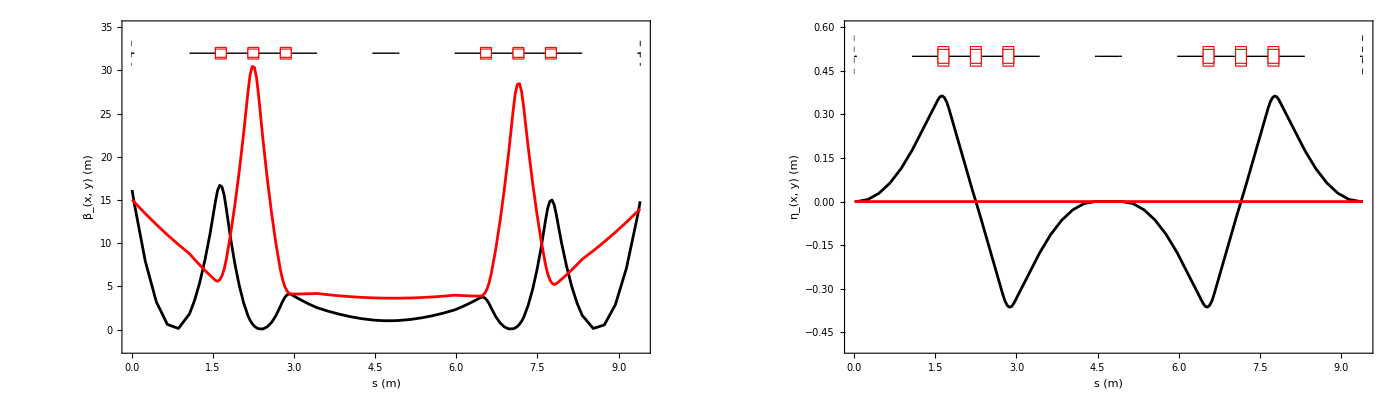

```mathematica
GraphicsRow[{mfsPlot[{{S,BETX},{S,BETY}},Prolog->MADDraw[MADFlatten[PartPathCorrector],Bends->False,WidthScale->4,Offset->32]⟦1⟧,Frame->True,LabelStyle->{FontSize->15,FontFamily->"Times"},FrameLabel->{"s (m)","β_(x, y) (m)","",""},AxesOrigin->{0,0},PlotRange->{All,{-2,35}}],mfsPlot[{{S,DX},{S,DY}},Prolog->MADDraw[MADFlatten[PartPathCorrector],Bends->False,WidthScale->0.2,Offset->0.5]⟦1⟧,Frame->True,LabelStyle->{FontSize->15,FontFamily->"Times"},FrameLabel->{"s (m)","η_(x, y) (m)","",""},PlotRange->{All,{-0.5,0.6}}]},ImageSize->1400]
```

good, that worked fine

```mathematica
Options[mfsPlot]={Joined->True,PlotStyle->{{AbsoluteThickness[3],Black,Dashing->False},{AbsoluteThickness[3],Black,AbsoluteDashing[6]},{AbsoluteThickness[3],Red,DotDashed},{AbsoluteThickness[2],Red,Dotted},{AbsoluteThickness[2],RGBColor[0.5,0.5,0.5]}}};
```

```mathematica
MLCS//Dimensions
```

{230}

```mathematica
MLCCumulativeRTMatrices[MADReadRMatrices["PartPathCorrector.sectormap.txt"],MADReadTMatrices["PartPathCorrector.sectormap.txt"]]⟦All,1,5,6⟧//Dimensions
```

{115}

compare MLC and MAD

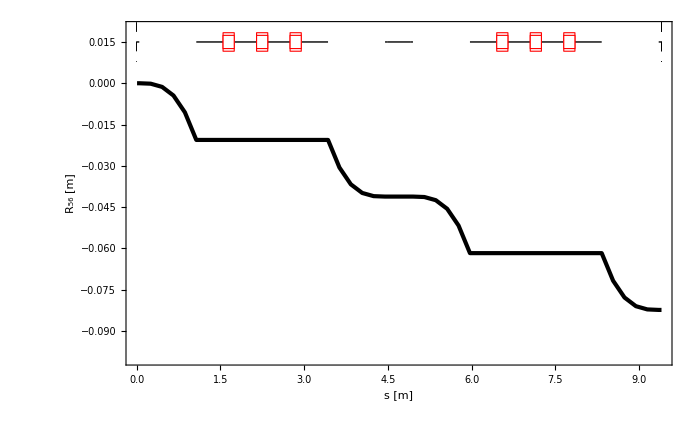

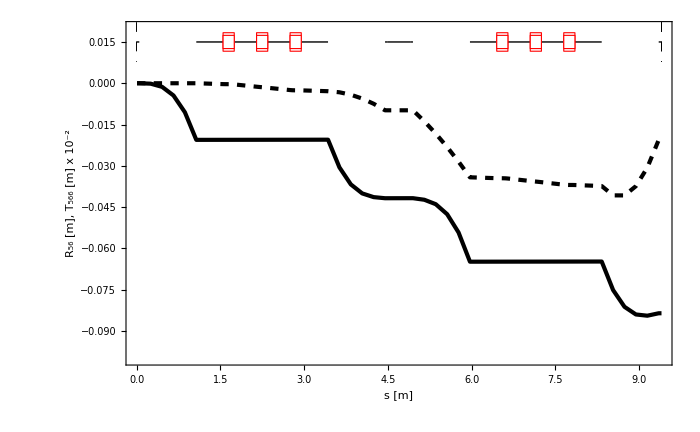

```mathematica
{MLCS=MADGetLengths[MADSplitElements[{PartPathCorrector},#]],MLCRpositive=Rest[MLCCumulativeRMatrices[MLCRMatrices[MADSplitElements[{PartPathCorrector},#]]]]}&[5];plot1=Show[mfsPlot[{{MLCS,(#[[5,6]]&/@MLCRpositive)}},PlotRange->{{0,Last[MLCS]},{-.1,0.02}}, Frame->True,GridLines->None,TextStyle->{FontFamily->"Times",PrivateFontOptions->{"FontPostScriptName"->Automatic},FontSize->25},FrameLabel->{"s [m]","R_56 [m]"},DisplayFunction->Identity],MADDraw[{PartPathCorrector},Bends->False,DisplayFunction->Identity,Offset->0.015,Labels->False,Thick->0.01,WidthScale->0.02],DisplayFunction->$DisplayFunction,ImageSize->700]
plot2=Show[mfsPlot[{{MLCS,MLCCumulativeRTMatrices[MADReadRMatrices["PartPathCorrector.sectormap.txt"],MADReadTMatrices["PartPathCorrector.sectormap.txt"]]⟦All,1,5,6⟧},{MLCS,MLCCumulativeRTMatrices[MADReadRMatrices["PartPathCorrector.sectormap.txt"],MADReadTMatrices["PartPathCorrector.sectormap.txt"]]⟦All,2,5,6,6⟧/100}},PlotRange->{{0,Last[MLCS]},{-.1,0.02}}, Frame->True,GridLines->None,TextStyle->{FontFamily->"Times",PrivateFontOptions->{"FontPostScriptName"->Automatic},FontSize->25},FrameLabel->{"s [m]","R_56 [m], T_566 [m] x 10^-2 "},DisplayFunction->Identity],MADDraw[{PartPathCorrector},Bends->False,DisplayFunction->Identity,Offset->0.015,Labels->False,Thick->0.01,WidthScale->0.02],DisplayFunction->$DisplayFunction,ImageSize->700]

(*mfsPlot[{{S,BETX},{S,BETY}},Prolog->MADDraw[MADFlatten[PartPathCorrector],Bends->False,WidthScale->4,Offset->17]⟦1⟧,Frame->True,LabelStyle->{FontSize->15,FontFamily->"Times"},FrameLabel->{"s (m)","β_(x, y) (m)","",""},AxesOrigin->{0,0},PlotRange->{All,{-2,20}}]*)
```

YES - this works!

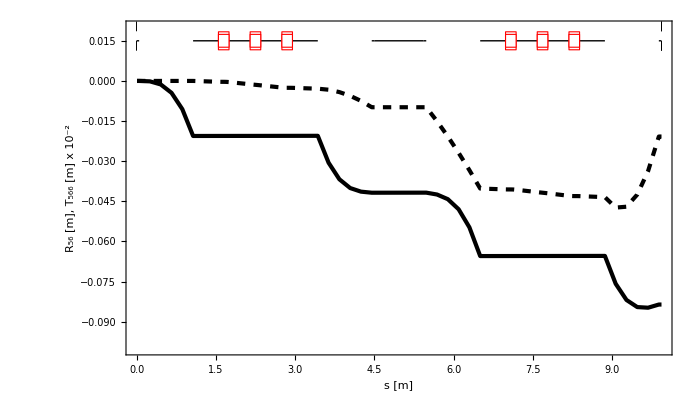

```mathematica
testplot=Show[plot2,ImageSize->700,Frame->True,GridLines->None,TextStyle->{FontFamily->"Times",PrivateFontOptions->{"FontPostScriptName"->Automatic},FontSize->25},FrameLabel->{"s [m]","R_56 [m], T_566 [m] x 10^-2 "},AspectRatio->0.6]
```

```mathematica
Export["fig_12_1p2.eps",testplot];Export["fig_12_1p2.png",testplot]
```

fig_12_1p2.png

Now add the chicane - use MAD matched values

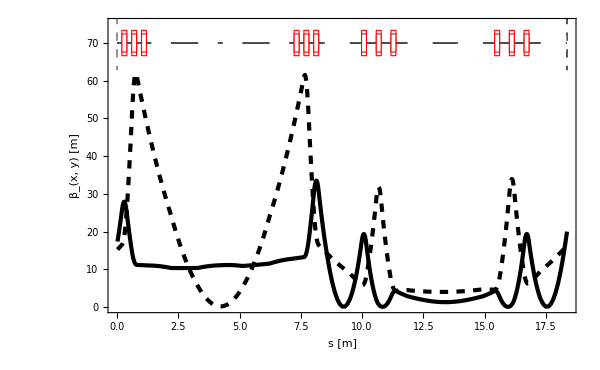

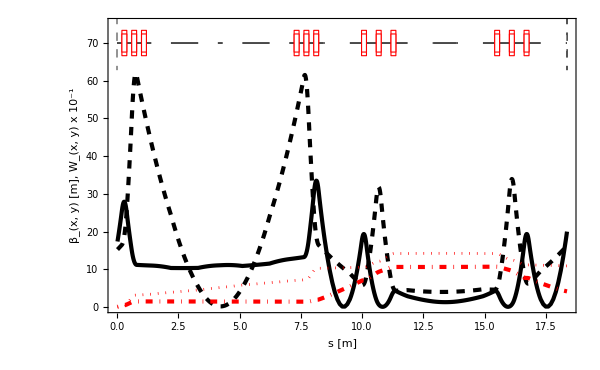

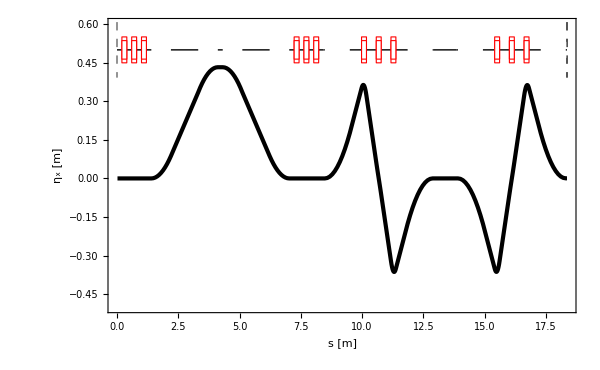

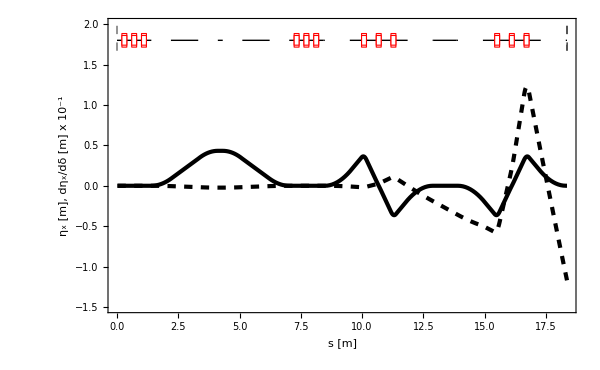

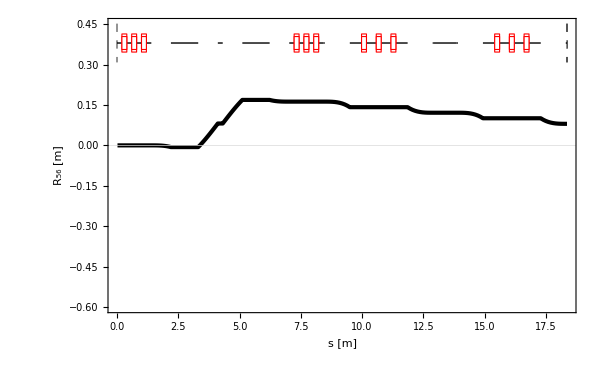

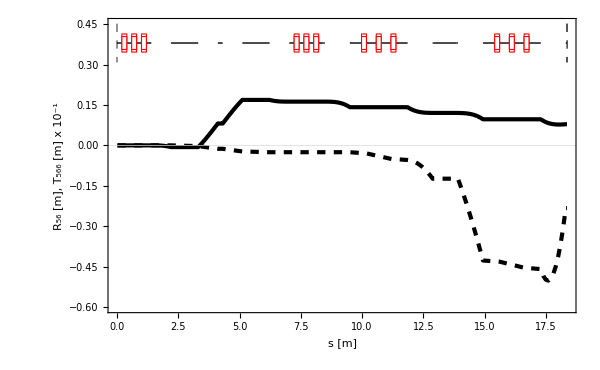

```mathematica
Subscript[θ, Dog]:=20. π/180.;
Subscript[L, DogExt]:=0.05;
Subscript[L, DD]:=0.5;
Subscript[L, NF]:=0.5+1(1-Subscript[θ, Dog]/Sin[Subscript[θ, Dog]]);
Subscript[ML, Dog]:=1 Subscript[θ, Dog]/Sin[Subscript[θ, Dog]];
Subscript[ML, Q1]:=0.2;
Subscript[ML, Q2]:=0.2;
Subscript[L, DDM]:=Subscript[L, DD]-Subscript[ML, Q2]/2;
drift[DDN,Subscript[L, NF],"DDN"];
drift[DD,Subscript[L, DD],"DD"];
drift[DDM,Subscript[L, DDM],"DDM"];
drift[DDE,Subscript[L, DogExt],"DDE"];
drift[DDMID,0.4+ 2 (2 Subscript[L, NF]+2 Subscript[ML, Dog]+2 Subscript[L, DDM]+2 Subscript[ML, Q1]+Subscript[ML, Q2])(1.-Cos[Subscript[θ, Dog]]),"DDMID"];
drift[DDMIDH,(0.4+ 2(2 Subscript[L, NF]+2 Subscript[ML, Dog]+2 Subscript[L, DDM]+2 Subscript[ML, Q1]+Subscript[ML, Q2])(1.-Cos[Subscript[θ, Dog]])-Subscript[ML, Q2])/2,"DDMIDH"];
sbend[BD4,Subscript[ML, Dog],0.0,Subscript[θ, Dog],"BD4",E1->0,E2->Subscript[θ, Dog]];
sbend[BD3,Subscript[ML, Dog],0.0,-Subscript[θ, Dog],"BD3",E1->-Subscript[θ, Dog],E2->0];
sbend[BD2,Subscript[ML, Dog],0.0,Subscript[θ, Dog],"BD2",E1->Subscript[θ, Dog],E2->0];
sbend[BD1,Subscript[ML, Dog],0.0,-Subscript[θ, Dog],"BD1",E1->0,E2->-Subscript[θ, Dog]];
quad[Q1,Subscript[ML, Q1],14.319867595222,"Q1"];
quad[Q2,Subscript[ML, Q2],-11.414757884601,"Q2"];
DogLegsq := {DDE,BD4,DDN,Q1,DDM,Q2,DDM,Q1,DDN,BD3,DDE};
RDogLegsq := {DDE,BD1,DDN,Q1,DDM,Q2,DDM,Q1,DDN,BD2,DDE};
PartPathCorrector={DogLegsq,DDMID,RDogLegsq};
Subscript[M, T]=Subscript[M, 1E1].Subscript[M, D].Subscript[M, 2E2].Subscript[M, D6].Subscript[M, 2E1].Subscript[M, D].Subscript[M, 1E2];
L1:=1.1 ;
L2:=0.2;
Subscript[ML, Chi]:=0.8;
R56Tot=0.08;
Subscript[θ, Chi]:= ToExpression[StringTake[ToString[FindRoot[ReplaceAll[Subscript[M, T][[5,6]],{Subscript[L, B]-> Subscript[ML, Chi],Subscript[L, D]->L1 Cos[0.15558]/Cos[θ],Subscript[L, D6]-> L2}]==(R56Tot-2 Last[MLCCumulativeRMatrices[MLCRMatrices[MADFlatten[DogLegsq]]]⟦All,5,6⟧]),{θ,20. π/180}]],{7,13}]];
drift[D1,L1 Cos[0.15558]/Cos[Subscript[θ, Chi]],"D1"];
drift[D2,L2,"D2"];
sbend[BC4,Subscript[ML, Chi],0.0,Subscript[θ, Chi],"BC2",E1->Subscript[θ, Chi],E2->0];
sbend[BC3,Subscript[ML, Chi],0.0,-Subscript[θ, Chi],"BC1",E1->0,E2->-Subscript[θ, Chi]];
sbend[BC2,Subscript[ML, Chi],0.0,-Subscript[θ, Chi],"BC1",E1->-Subscript[θ, Chi],E2->0];
sbend[BC1,Subscript[ML, Chi],0.0,Subscript[θ, Chi],"BC2",E1->0,E2->Subscript[θ, Chi]];
quad[Q4,Subscript[ML, Q1],10.0480598562,"Q4"];
quad[Q5,Subscript[ML, Q1],-7.755050845629,"Q5"];
quad[Q6,Subscript[ML, Q1],0,"Q6"];
Chicane:={D2,Q4,D2,Q5,D2,Q6,D2,BC1,D1,BC2,D2,BC3,D1,BC4,D2,Q6,D2,Q5,D2,Q4,D2};
FullPathCorrector:={Chicane,PartPathCorrector};
spti:={MLCBetaGamma[16.556188280129,-20],MLCBetaGamma[15.09640707461,-3.39270267421]};;
spdi:={0,0,0,0,0,1};
(* Do This in MAD aswell *)
MADWrite["FullPathCorrector",MADSplitElements[{FullPathCorrector},10]]
MADStringWrite["FullPathCorrector","eopt,add;\nINITIAL:BETA0,&\n
 BETX="<>ToString[spti⟦1,1⟧]<>",ALFX="<>ToString[spti⟦1,2⟧]<>",&\n
 BETY="<>ToString[spti⟦2,1⟧]<>",ALFY="<>ToString[spti⟦2,2⟧]<>",&\n
dx=0,dpx=0;\n"];MADStringWrite["FullPathCorrector","option,double;\nBEAM,PARTICLE=electron,PC="<>ToString[1.2]<>";\n"];
MADStringWrite["FullPathCorrector","select,optics,full;\noptics,beta0=initial,&\nfilename=optics.txt,columns=name,s,betx,bety,dx,alfx,&\nalfy,mux,muy,dpx,dy,dpy,&\nwx,wy,ddx,ddy,ddpx,ddpy;\n
sectormap,filename=\"FullPathCorrector.sectormap.txt\",deltap=0.001\n
select twiss,full\n"];
ReadList["!mad8.exe < FullPathCorrector.mff",Word];
mfsInterpret["optics.txt",mfsVerbose->False];
(* end MAD bit *)
{MLCElems,MLCS,MLCBETX,MLCALFX,MLCGAMX,MLCBETY,MLCALFY,MLCGAMY,MLCMUX,MLCMUY,MLCDX,MLCDPX,MLCDY,MLCDPY}=
MLCGenerateTwissTable[MADSplitElements[FullPathCorrector,10],spti,{0,0},spdi];plot7=Show[mfsPlot[{{MLCS,MLCBETX},{MLCS,MLCBETY}},PlotRange->{{0,Last[MLCS]},{0,75}}, Frame->True,GridLines->None,TextStyle->{FontFamily->"Times",PrivateFontOptions->{"FontPostScriptName"->Automatic},FontSize->25},FrameLabel->{"s [m]","β_(x, y) [m]"},DisplayFunction-> Identity],MADDraw[{FullPathCorrector},Bends->False,DisplayFunction->Identity,Offset->70,Labels->False,Thick->0.001, WidthScale->20],DisplayFunction->$DisplayFunction,ImageSize->600]

plot7b=Show[mfsPlot[{{MLCS,BETX},{MLCS,BETY},{MLCS,WX/10},{MLCS,WY/10}},PlotRange->{{0,Last[MLCS]},{0,75}}, Frame->True,GridLines->None,TextStyle->{FontFamily->"Times",PrivateFontOptions->{"FontPostScriptName"->Automatic},FontSize->25},FrameLabel->{"s [m]","β_(x, y) [m], W_(x, y) x 10^-1 "},DisplayFunction->Identity],MADDraw[{FullPathCorrector},Bends->False,DisplayFunction->Identity,Offset->70,Labels->False,Thick->0.01,WidthScale->20],DisplayFunction->$DisplayFunction,ImageSize->600]

plot8=Show[mfsPlot[{{MLCS,MLCDX}},PlotRange->{{0,Last[MLCS]},{-0.5,.6}}, Frame->True,GridLines->None,TextStyle->{FontFamily->"Times",PrivateFontOptions->{"FontPostScriptName"->Automatic},FontSize->25},FrameLabel->{"s [m]","η_x [m]"},DisplayFunction->Identity],MADDraw[{FullPathCorrector},Bends->False,DisplayFunction->Identity,Offset->0.5,Labels->False,Thick->0.001,WidthScale->0.3],DisplayFunction->$DisplayFunction,ImageSize->600]

(*plot8b=Show[mfsPlot[{{MLCS,DX},{MLCS,MLCCumulativeRTMatrices[MADReadRMatrices["FullPathCorrector.sectormap.txt"],MADReadTMatrices["FullPathCorrector.sectormap.txt"]]⟦All,2,1,6,6⟧/10},{MLCS,DDX/20}},PlotRange->{{0,Last[MLCS]},{-2,2.5}}, Frame->True,GridLines->None,TextStyle->{FontFamily->"Times",PrivateFontOptions->{"FontPostScriptName"->Automatic},FontSize->25},FrameLabel->{"s [m]","η_x [m], T_166 [m] x 10^-1, dD_x/dδ [m] x 10^-1 "},DisplayFunction->Identity],MADDraw[{FullPathCorrector},Bends->False,DisplayFunction->Identity,Offset->2.2,Labels->False,Thick->0.001,WidthScale->0.5],DisplayFunction->$DisplayFunction,ImageSize->600]*)
plot8b=Show[mfsPlot[{{MLCS,DX},{MLCS,DDX/20}},PlotRange->{{0,Last[MLCS]},{-1.5,2.}}, Frame->True,GridLines->None,TextStyle->{FontFamily->"Times",PrivateFontOptions->{"FontPostScriptName"->Automatic},FontSize->25},FrameLabel->{"s [m]","η_x [m], dη_x/dδ [m] x 10^-1 "},DisplayFunction->Identity],MADDraw[{FullPathCorrector},Bends->False,DisplayFunction->Identity,Offset->1.8,Labels->False,Thick->0.001,WidthScale->0.5],DisplayFunction->$DisplayFunction,ImageSize->600]

{MLCS=MADGetLengths[MADSplitElements[{FullPathCorrector},#]],MLCRpositive=Rest[MLCCumulativeRMatrices[MLCRMatrices[MADSplitElements[{FullPathCorrector},#]]]]}&[10];plot9=Show[mfsPlot[{{MLCS,(#[[5,6]]&/@MLCRpositive)}},PlotRange->{{0,Last[MLCS]},{-0.6,0.45}}, Frame->True,GridLines->{None,{0}},TextStyle->{FontFamily->"Times",PrivateFontOptions->{"FontPostScriptName"->Automatic},FontSize->25},FrameLabel->{"s [m]","R_56 [m]"},DisplayFunction->Identity],MADDraw[{FullPathCorrector},Bends->False,DisplayFunction->Identity,Offset->0.38,Labels->False,Thick->0.001,WidthScale->0.2],DisplayFunction->$DisplayFunction,ImageSize->600]

plot9b=Show[mfsPlot[{{MLCS,MLCCumulativeRTMatrices[MADReadRMatrices["FullPathCorrector.sectormap.txt"],MADReadTMatrices["FullPathCorrector.sectormap.txt"]]⟦All,1,5,6⟧},{MLCS,MLCCumulativeRTMatrices[MADReadRMatrices["FullPathCorrector.sectormap.txt"],MADReadTMatrices["FullPathCorrector.sectormap.txt"]]⟦All,2,5,6,6⟧/10}},PlotRange->{{0,Last[MLCS]},{-0.6,0.45}}, Frame->True,GridLines->{None,{0}},TextStyle->{FontFamily->"Times",PrivateFontOptions->{"FontPostScriptName"->Automatic},FontSize->25},FrameLabel->{"s [m]","R_56 [m], T_566 [m] x 10^-1 "},DisplayFunction->Identity],MADDraw[{FullPathCorrector},Bends->False,DisplayFunction->Identity,Offset->0.38,Labels->False,Thick->0.001,WidthScale->0.2],DisplayFunction->$DisplayFunction,ImageSize->600]
```

```mathematica
Subscript[θ, Chi]
```

0.21894

Great!

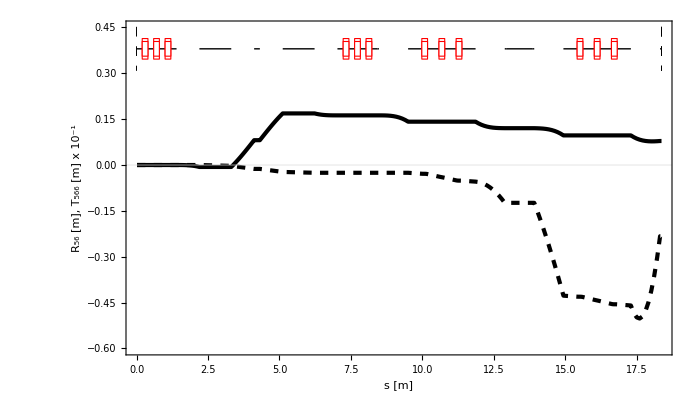

```mathematica
testplot=Show[plot9b,ImageSize->700,Frame->True,AspectRatio->0.6]
```

```mathematica
Export["r561200max.eps",testplot];Export["r561200max.png",testplot]
```

r561200max.png

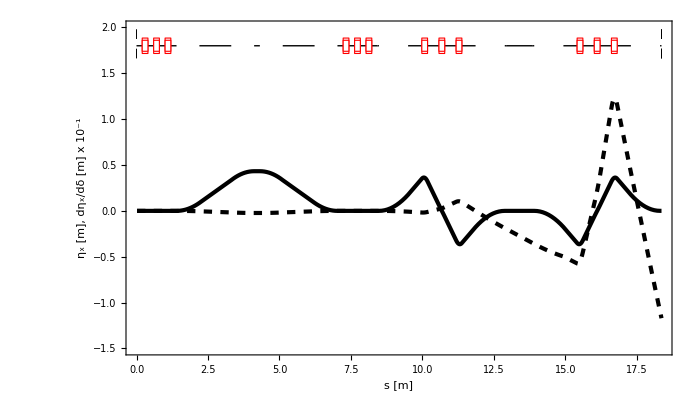

```mathematica
testplot=Show[plot8b,ImageSize->700,Frame->True,GridLines->None,AspectRatio->0.6]
```

```mathematica
Export["fig_13_1p2.eps",testplot];Export["fig_13_1p2.png",testplot]
```

fig_13_1p2.png

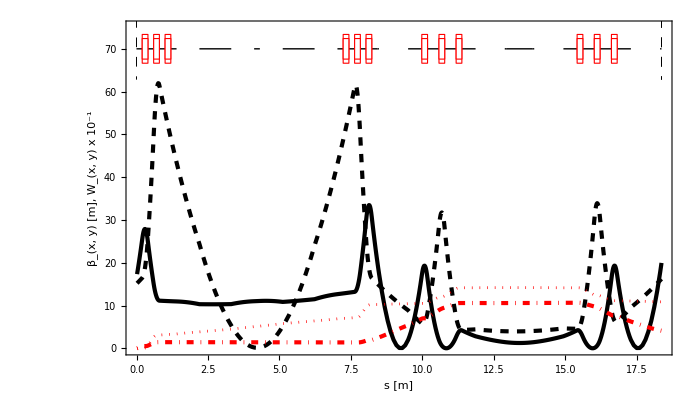

```mathematica
testplot=Show[plot7b,ImageSize->700,Frame->True,GridLines->None,AspectRatio->0.6]
```

```mathematica
Export["fig_15_1p2.eps",testplot];Export["fig_15_1p2.png",testplot]
```

fig_15_1p2.png

```mathematica
Options[MADDraw]={Labels->False,Thickness->0.001,Monitors->True,Lengths->False,Filled->False,WidthScale->1.4,Symms->True,Bends->True,Offset->0,ShowPicture->True,Fontsize->12,Imagesize->800,DrawLabel->"",CheckClosed->False,Frame->True}
```

{Labels→False,Thickness→0.001,Monitors→True,Lengths→False,Filled→False,WidthScale→1.4,Symms→True,Bends→True,Offset→0,ShowPicture→True,Fontsize→12,Imagesize→800,DrawLabel→,CheckClosed→False,Frame→True}

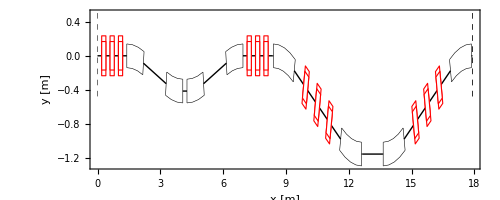

```mathematica
plot4=MADDraw[FullPathCorrector,Imagesize->700,Frame->True,GridLines->None,TextStyle->{FontFamily->"Courier",FontSize->12},FrameLabel->{"x [m]","y [m]"}]
```

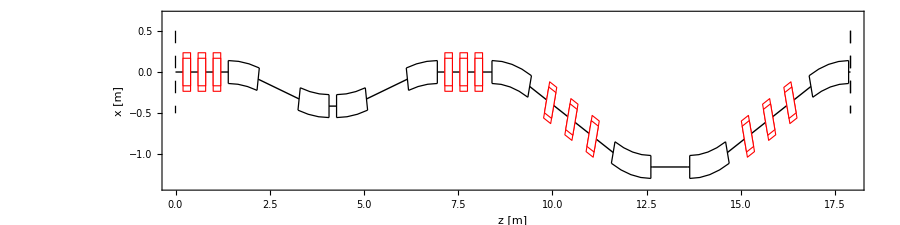

```mathematica
testplot=Show[plot4,ImageSize->900,Frame->True,GridLines->None,PlotRange->{Automatic,{-1.4,0.7}},TextStyle->{FontFamily-> "Times",PrivateFontOptions->{"FontPostScriptName"->Automatic},FontSize->25},FrameLabel->{"z [m]","x [m]"},AspectRatio->0.25]
```

```mathematica
Export["fig_10_1p2.eps",testplot];Export["fig_10_1p2.png",testplot]
```

fig_10_1p2.png

```mathematica
MADInfo[FullPathCorrector]
```

| Name | Element | Length | Focus | VAngle | HAngle | Type | Position
1 | D2 | Drift | 0.2 | --- | --- | --- | D2 | 0.2
2 | Q4 | Quadrupole | 0.2 | 10.0481 | --- | --- | Q4 | 0.4
3 | D2 | Drift | 0.2 | --- | --- | --- | D2 | 0.6
4 | Q5 | Quadrupole | 0.2 | -7.75505 | --- | --- | Q5 | 0.8
5 | D2 | Drift | 0.2 | --- | --- | --- | D2 | 1.
6 | Q6 | Quadrupole | 0.2 | 0 | --- | --- | Q6 | 1.2
7 | D2 | Drift | 0.2 | --- | --- | --- | D2 | 1.4
8 | BC1 | SectorBend | 0.8 | 0. | --- | 0.21894 | BC2 | 2.2
9 | D1 | Drift | 1.11329 | --- | --- | --- | D1 | 3.31329
10 | BC2 | SectorBend | 0.8 | 0. | --- | -0.21894 | BC1 | 4.11329
11 | D2 | Drift | 0.2 | --- | --- | --- | D2 | 4.31329
12 | BC3 | SectorBend | 0.8 | 0. | --- | -0.21894 | BC1 | 5.11329
13 | D1 | Drift | 1.11329 | --- | --- | --- | D1 | 6.22658
14 | BC4 | SectorBend | 0.8 | 0. | --- | 0.21894 | BC2 | 7.02658
15 | D2 | Drift | 0.2 | --- | --- | --- | D2 | 7.22658
16 | Q6 | Quadrupole | 0.2 | 0 | --- | --- | Q6 | 7.42658
17 | D2 | Drift | 0.2 | --- | --- | --- | D2 | 7.62658
18 | Q5 | Quadrupole | 0.2 | -7.75505 | --- | --- | Q5 | 7.82658
19 | D2 | Drift | 0.2 | --- | --- | --- | D2 | 8.02658
20 | Q4 | Quadrupole | 0.2 | 10.0481 | --- | --- | Q4 | 8.22658
21 | D2 | Drift | 0.2 | --- | --- | --- | D2 | 8.42658
22 | DDE | Drift | 0.05 | --- | --- | --- | DDE | 8.47658
23 | BD4 | SectorBend | 1.0206 | 0. | --- | 0.349066 | BD4 | 9.49718
24 | DDN | Drift | 0.4794 | --- | --- | --- | DDN | 9.97658
25 | Q1 | Quadrupole | 0.2 | 14.3199 | --- | --- | Q1 | 10.1766
26 | DDM | Drift | 0.4 | --- | --- | --- | DDM | 10.5766
27 | Q2 | Quadrupole | 0.2 | -11.4148 | --- | --- | Q2 | 10.7766
28 | DDM | Drift | 0.4 | --- | --- | --- | DDM | 11.1766
29 | Q1 | Quadrupole | 0.2 | 14.3199 | --- | --- | Q1 | 11.3766
30 | DDN | Drift | 0.4794 | --- | --- | --- | DDN | 11.856
31 | BD3 | SectorBend | 1.0206 | 0. | --- | -0.349066 | BD3 | 12.8766
32 | DDE | Drift | 0.05 | --- | --- | --- | DDE | 12.9266
33 | DDMID | Drift | 0.930705 | --- | --- | --- | DDMID | 13.8573
34 | DDE | Drift | 0.05 | --- | --- | --- | DDE | 13.9073
35 | BD1 | SectorBend | 1.0206 | 0. | --- | -0.349066 | BD1 | 14.9279
36 | DDN | Drift | 0.4794 | --- | --- | --- | DDN | 15.4073
37 | Q1 | Quadrupole | 0.2 | 14.3199 | --- | --- | Q1 | 15.6073
38 | DDM | Drift | 0.4 | --- | --- | --- | DDM | 16.0073
39 | Q2 | Quadrupole | 0.2 | -11.4148 | --- | --- | Q2 | 16.2073
40 | DDM | Drift | 0.4 | --- | --- | --- | DDM | 16.6073
41 | Q1 | Quadrupole | 0.2 | 14.3199 | --- | --- | Q1 | 16.8073
42 | DDN | Drift | 0.4794 | --- | --- | --- | DDN | 17.2867
43 | BD2 | SectorBend | 1.0206 | 0. | --- | 0.349066 | BD2 | 18.3073
44 | DDE | Drift | 0.05 | --- | --- | --- | DDE | 18.3573

Total Length = 18.3573 m

### Beta function Matched Path Corrector - Square Case - Min Position

Below uses MAD matching values

0.15544

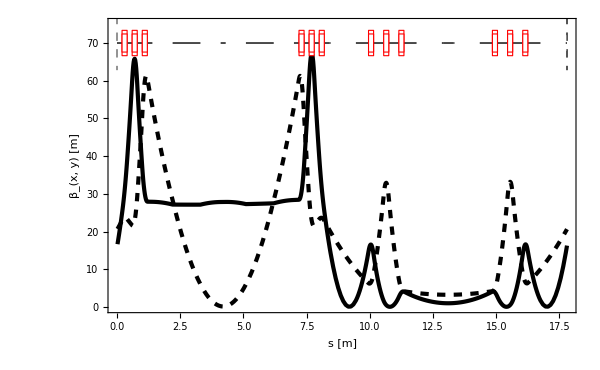

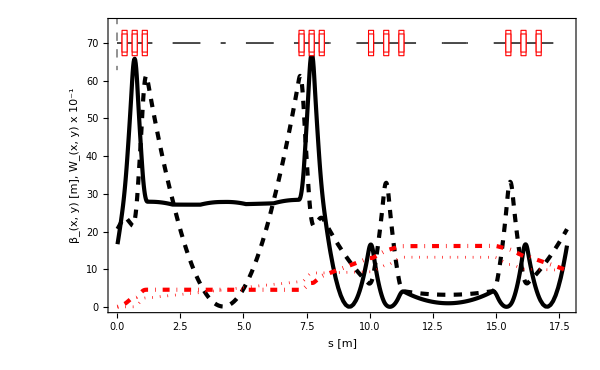

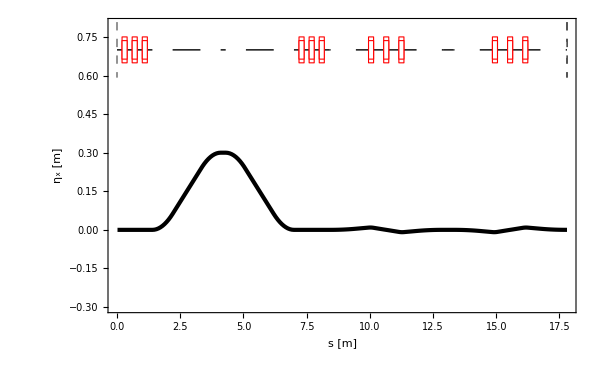

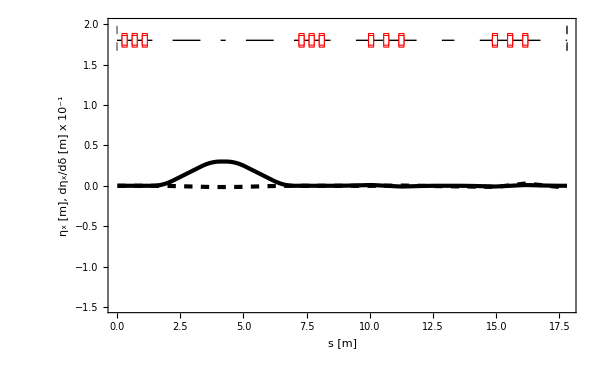

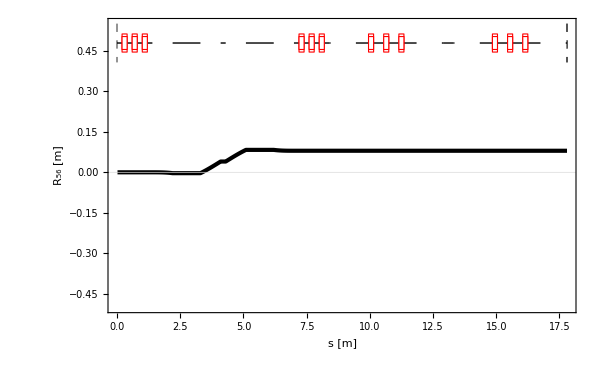

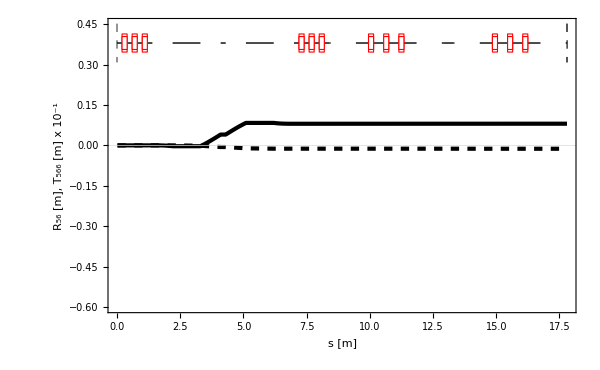

```mathematica
Subscript[θ, Dog]:=0.5 π/180.;
Subscript[L, DogExt]:=0.05;
Subscript[L, DD]:=0.5;
Subscript[L, NF]:=0.5+1(1-Subscript[θ, Dog]/Sin[Subscript[θ, Dog]]);
Subscript[ML, Dog]:=1 Subscript[θ, Dog]/Sin[Subscript[θ, Dog]];
Subscript[ML, Q1]:=0.2;
Subscript[ML, Q2]:=0.2;
Subscript[L, DDM]:=Subscript[L, DD]-Subscript[ML, Q2]/2;
drift[DDN,Subscript[L, NF],"DDN"];
drift[DD,Subscript[L, DD],"DD"];
drift[DDM,Subscript[L, DDM],"DDM"];
drift[DDE,Subscript[L, DogExt],"DDE"];
drift[DDMID,0.4+ 2 (2 Subscript[L, NF]+2 Subscript[ML, Dog]+2 Subscript[L, DDM]+2 Subscript[ML, Q1]+Subscript[ML, Q2])(1.-Cos[Subscript[θ, Dog]]),"DDMID"];
drift[DDMIDH,(0.4+ 2(2 Subscript[L, NF]+2 Subscript[ML, Dog]+2 Subscript[L, DDM]+2 Subscript[ML, Q1]+Subscript[ML, Q2])(1.-Cos[Subscript[θ, Dog]])-Subscript[ML, Q2])/2,"DDMIDH"];
sbend[BD4,Subscript[ML, Dog],0.0,Subscript[θ, Dog],"BD4",E1->0,E2->Subscript[θ, Dog]];
sbend[BD3,Subscript[ML, Dog],0.0,-Subscript[θ, Dog],"BD3",E1->-Subscript[θ, Dog],E2->0];
sbend[BD2,Subscript[ML, Dog],0.0,Subscript[θ, Dog],"BD2",E1->Subscript[θ, Dog],E2->0];
sbend[BD1,Subscript[ML, Dog],0.0,-Subscript[θ, Dog],"BD1",E1->0,E2->-Subscript[θ, Dog]];
quad[Q1,Subscript[ML, Q1],14.13688299921,"Q1"];
quad[Q2,Subscript[ML, Q2],-11.423878553066,"Q2"];
DogLegsq := {DDE,BD4,DDN,Q1,DDM,Q2,DDM,Q1,DDN,BD3,DDE};
RDogLegsq := {DDE,BD1,DDN,Q1,DDM,Q2,DDM,Q1,DDN,BD2,DDE};
PartPathCorrectorMin={DogLegsq,DDMID,RDogLegsq};
Subscript[M, T]=Subscript[M, 1E1].Subscript[M, D].Subscript[M, 2E2].Subscript[M, D6].Subscript[M, 2E1].Subscript[M, D].Subscript[M, 1E2];
L1:=1.1 ;
L2:=0.2;
Subscript[ML, Chi]:=0.8;
R56Tot=0.08;
Subscript[θ, Chi]:= ToExpression[StringTake[ToString[FindRoot[ReplaceAll[Subscript[M, T][[5,6]],{Subscript[L, B]-> Subscript[ML, Chi],Subscript[L, D]->L1 Cos[0.15558]/Cos[θ],Subscript[L, D6]-> L2}]==(R56Tot-2 Last[MLCCumulativeRMatrices[MLCRMatrices[MADFlatten[DogLegsq]]]⟦All,5,6⟧]),{θ,20. π/180}]],{7,13}]];
Print[Subscript[θ, Chi]];
drift[D1,L1 Cos[0.15558]/Cos[Subscript[θ, Chi]],"D1"];
drift[D2,L2,"D2"];
sbend[BC4,Subscript[ML, Chi],0.0,Subscript[θ, Chi],"BC2",E1->Subscript[θ, Chi],E2->0];
sbend[BC3,Subscript[ML, Chi],0.0,-Subscript[θ, Chi],"BC1",E1->0,E2->-Subscript[θ, Chi]];
sbend[BC2,Subscript[ML, Chi],0.0,-Subscript[θ, Chi],"BC1",E1->-Subscript[θ, Chi],E2->0];
sbend[BC1,Subscript[ML, Chi],0.0,Subscript[θ, Chi],"BC2",E1->0,E2->Subscript[θ, Chi]];
quad[Q4,Subscript[ML, Q1],-2.272330262842,"Q4"];
quad[Q5,Subscript[ML, Q1],9.800468854141,"Q5"];
quad[Q6,Subscript[ML, Q1],-7.27668624247,"Q1"];
Chicane:={D2,Q4,D2,Q5,D2,Q6,D2,BC1,D1,BC2,D2,BC3,D1,BC4,D2,Q6,D2,Q5,D2,Q4,D2};
FullPathCorrectorMin:={Chicane,PartPathCorrectorMin};
spti:={MLCBetaGamma[15.844334369225,-19.99999987815],MLCBetaGamma[20.45629238788,-5.947395346354]};
spdi:={0,0,0,0,0,1};
(* Do This in MAD aswell *)
MADWrite["FullPathCorrectorMin",MADSplitElements[{FullPathCorrectorMin},10]]
MADStringWrite["FullPathCorrectorMin","eopt,add;\nINITIAL:BETA0,&\n
 BETX="<>ToString[spti⟦1,1⟧]<>",ALFX="<>ToString[spti⟦1,2⟧]<>",&\n
 BETY="<>ToString[spti⟦2,1⟧]<>",ALFY="<>ToString[spti⟦2,2⟧]<>",&\n
dx=0,dpx=0;\n"];MADStringWrite["FullPathCorrectorMin","option,double;\nBEAM,PARTICLE=electron,PC="<>ToString[0.1]<>";\n"];
MADStringWrite["FullPathCorrectorMin","select,optics,full;\noptics,beta0=initial,&\nfilename=optics.txt,columns=name,s,betx,bety,dx,alfx,&\nalfy,mux,muy,dpx,dy,dpy,&\nwx,wy,ddx,ddy,ddpx,ddpy;\n
sectormap,filename=\"FullPathCorrectorMin.sectormap.txt\",deltap=0.001\n
select twiss,full\n"];
ReadList["!mad8.exe < FullPathCorrectorMin.mff",Word];
mfsInterpret["optics.txt",mfsVerbose->False];
(* end MAD bit *)
{MLCElems,MLCS,MLCBETX,MLCALFX,MLCGAMX,MLCBETY,MLCALFY,MLCGAMY,MLCMUX,MLCMUY,MLCDX,MLCDPX,MLCDY,MLCDPY}=
MLCGenerateTwissTable[MADSplitElements[FullPathCorrectorMin,10],spti,{0,0},spdi];plot7=Show[mfsPlot[{{MLCS,MLCBETX},{MLCS,MLCBETY}},PlotRange->{{0,Last[MLCS]},{0,75}}, Frame->True,GridLines->None,TextStyle->{FontFamily->"Times",PrivateFontOptions->{"FontPostScriptName"->Automatic},FontSize->25},FrameLabel->{"s [m]","β_(x, y) [m]"},DisplayFunction-> Identity],MADDraw[{FullPathCorrectorMin},Bends->False,DisplayFunction->Identity,Offset->70,Labels->False,Thick->0.001, WidthScale->20],DisplayFunction->$DisplayFunction,ImageSize->600]

plot7b=Show[mfsPlot[{{MLCS,BETX},{MLCS,BETY},{MLCS,WX/10},{MLCS,WY/10}},PlotRange->{{0,Last[MLCS]},{0,75}}, Frame->True,GridLines->None,TextStyle->{FontFamily->"Times",PrivateFontOptions->{"FontPostScriptName"->Automatic},FontSize->25},FrameLabel->{"s [m]","β_(x, y) [m], W_(x, y) x 10^-1 "},DisplayFunction->Identity],MADDraw[{FullPathCorrector},Bends->False,DisplayFunction->Identity,Offset->70,Labels->False,Thick->0.01,WidthScale->20],DisplayFunction->$DisplayFunction,ImageSize->600]

plot8=Show[mfsPlot[{{MLCS,MLCDX}},PlotRange->{{0,Last[MLCS]},{-0.3,.8}}, Frame->True,GridLines->None,TextStyle->{FontFamily->"Times",PrivateFontOptions->{"FontPostScriptName"->Automatic},FontSize->25},FrameLabel->{"s [m]","η_x [m]"},DisplayFunction->Identity],MADDraw[{FullPathCorrectorMin},Bends->False,DisplayFunction->Identity,Offset->0.7,Labels->False,Thick->0.001,WidthScale->0.3],DisplayFunction->$DisplayFunction,ImageSize->600]

plot8b=Show[mfsPlot[{{MLCS,DX},{MLCS,DDX/20}},PlotRange->{{0,Last[MLCS]},{-1.5,2}}, Frame->True,GridLines->None,TextStyle->{FontFamily->"Times",PrivateFontOptions->{"FontPostScriptName"->Automatic},FontSize->25},FrameLabel->{"s [m]","η_x [m], dη_x/dδ [m] x 10^-1 "},DisplayFunction->Identity],MADDraw[{FullPathCorrectorMin},Bends->False,DisplayFunction->Identity,Offset->1.8,Labels->False,Thick->0.001,WidthScale->0.5],DisplayFunction->$DisplayFunction,ImageSize->600]

{MLCS=MADGetLengths[MADSplitElements[{FullPathCorrectorMin},#]],MLCRpositive=Rest[MLCCumulativeRMatrices[MLCRMatrices[MADSplitElements[{FullPathCorrectorMin},#]]]]}&[10];plot9=Show[mfsPlot[{{MLCS,(#[[5,6]]&/@MLCRpositive)}},PlotRange->{{0,Last[MLCS]},{-0.5,0.55}}, Frame->True,GridLines->{None,{0}},TextStyle->{FontFamily->"Times",PrivateFontOptions->{"FontPostScriptName"->Automatic},FontSize->25},FrameLabel->{"s [m]","R_56 [m]"},DisplayFunction->Identity],MADDraw[{FullPathCorrectorMin},Bends->False,DisplayFunction->Identity,Offset->0.48,Labels->False,Thick->0.001,WidthScale->0.2],DisplayFunction->$DisplayFunction,ImageSize->600]

plot9b=Show[mfsPlot[{{MLCS,MLCCumulativeRTMatrices[MADReadRMatrices["FullPathCorrectorMin.sectormap.txt"],MADReadTMatrices["FullPathCorrectorMin.sectormap.txt"]]⟦All,1,5,6⟧},{MLCS,MLCCumulativeRTMatrices[MADReadRMatrices["FullPathCorrectorMin.sectormap.txt"],MADReadTMatrices["FullPathCorrectorMin.sectormap.txt"]]⟦All,2,5,6,6⟧/10}},PlotRange->{{0,Last[MLCS]},{-0.6,0.45}}, Frame->True,GridLines->{None,{0}},TextStyle->{FontFamily->"Times",PrivateFontOptions->{"FontPostScriptName"->Automatic},FontSize->25},FrameLabel->{"s [m]","R_56 [m], T_566 [m] x 10^-1 "},DisplayFunction->Identity],MADDraw[{FullPathCorrectorMin},Bends->False,DisplayFunction->Identity,Offset->0.38,Labels->False,Thick->0.001,WidthScale->0.2],DisplayFunction->$DisplayFunction,ImageSize->600]
```

Great!

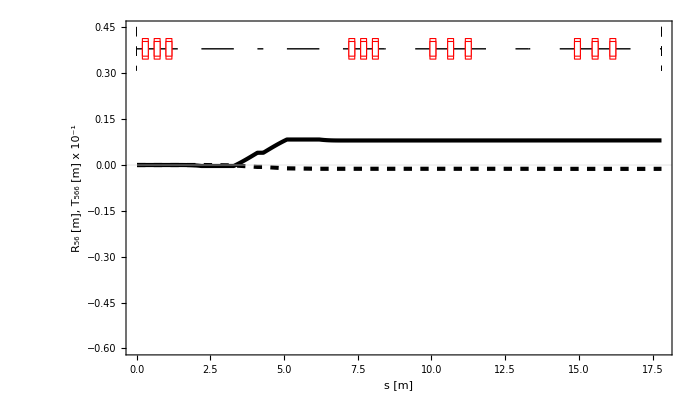

```mathematica
testplot=Show[plot9b,ImageSize->700,Frame->True,AspectRatio->0.6]
```

```mathematica
Export["fig_14_min_1p2.eps",testplot];Export["fig_14_min_1p2.png",testplot]
```

fig_14_min_1p2.png

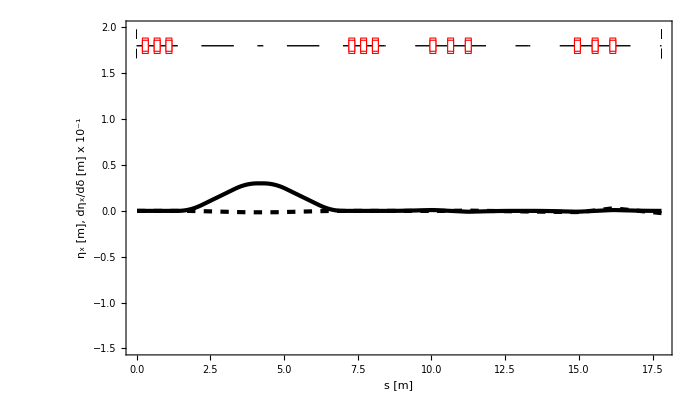

```mathematica
testplot=Show[plot8b,ImageSize->700,Frame->True,GridLines->None,AspectRatio->0.6]
```

```mathematica
Export["fig_13_min_1p2.eps",testplot];Export["fig_13_min1p2.png",testplot]
```

fig_13_min1p2.png

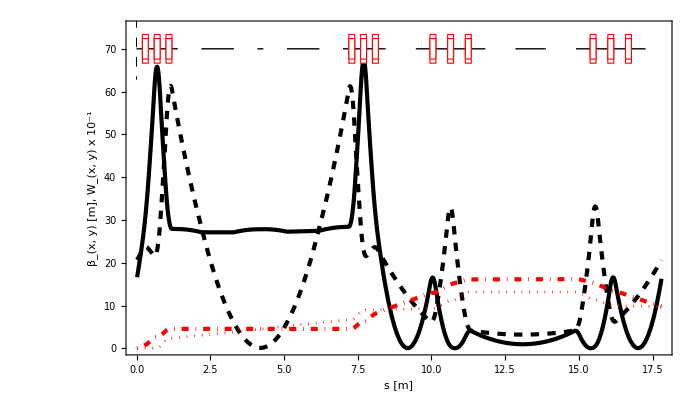

```mathematica
testplot=Show[plot7b,ImageSize->700,Frame->True,GridLines->None,AspectRatio->0.6]
```

```mathematica
Export["fig_15_min_1p2.eps",testplot];Export["fig_15_min_1p2.png",testplot]
```

fig_15_min_1p2.png

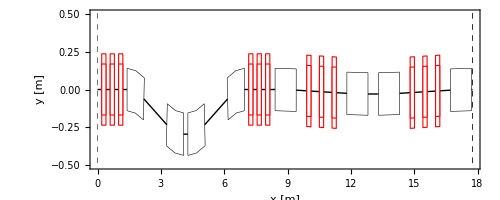

```mathematica
plot4=MADDraw[FullPathCorrectorMin,Imagesize->700,Frame->True,GridLines->None,TextStyle->{FontFamily->"Courier",FontSize->12},FrameLabel->{"x [m]","y [m]"}]
```

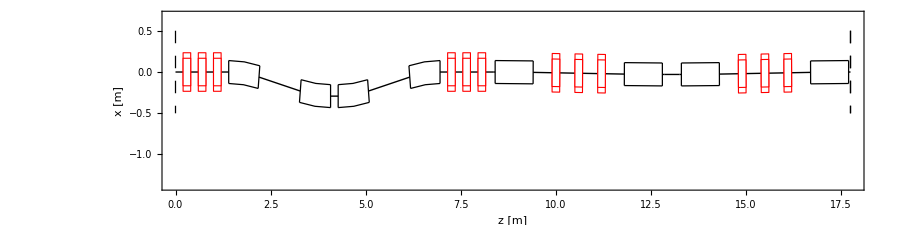

```mathematica
testplot=Show[plot4,ImageSize->900,Frame->True,GridLines->None,PlotRange->{Automatic,{-1.4,0.7}},TextStyle->{FontFamily-> "Times",PrivateFontOptions->{"FontPostScriptName"->Automatic},FontSize->25},FrameLabel->{"z [m]","x [m]"},AspectRatio->0.25]
```

```mathematica
Export["fig_9_1p2.eps",testplot];Export["fig_9_1p2.png",testplot]
```

fig_9_1p2.png

### Emittance Growth

Here is synchrotron H function

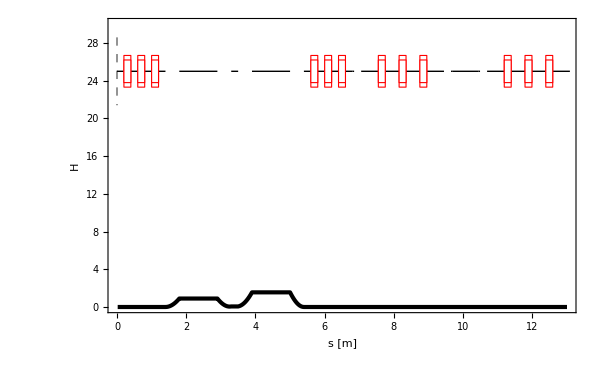

```mathematica
Show[mfsPlot[{{MLCS,MLCBETX MLCDPX^2 + 2 MLCALFX MLCDX MLCDPX + MLCGAMX MLCDX^2}},PlotRange->{{0,Last[MLCS]},{0,30.0}}, Frame->True,GridLines->None,TextStyle->{FontFamily->"Courier",FontSize->12},FrameLabel->{"s [m]","H"},DisplayFunction-> Identity],MADDraw[{FullPathCorrector},Bends->False,DisplayFunction->Identity,Offset->25,Labels->False,Thick->0.001,WidthScale->10],DisplayFunction->$DisplayFunction,ImageSize->600]
```

This is a list of α,β,γ, dispersion and derivative for each section - for x-plane.

```mathematica
tmat=Transpose[MLCGenerateTwissTable[MADSplitElements[{FullPathCorrector},10],spti,{0,0},spdi]⟦{3,4,5,11,12}⟧];
```

This is the position of the sectorbends

```mathematica
pos=(Position[MADFlatten[MADSplitElements[{FullPathCorrector},10]],"SectorBend"]⟦All,1⟧-1)
```

{70,71,72,73,74,75,76,77,78,79,90,91,92,93,94,95,96,97,98,99,110,111,112,113,114,115,116,117,118,119,130,131,132,133,134,135,136,137,138,139,220,221,222,223,224,225,226,227,228,229,300,301,302,303,304,305,306,307,308,309,340,341,342,343,344,345,346,347,348,349,420,421,422,423,424,425,426,427,428,429}

```mathematica
myMLCSRI5H[{elem_,input1_}]:=Module[{kx,ky,ρ, h, n,L},
Plus@@((L=#⟦1,3⟧;ρ=L/#⟦1,6⟧;n=-#⟦1,4⟧ ρ^2;h=1/ρ;kx=h Sqrt[1-n];ky=h Sqrt[n];If[kx=!=0,myintegralSRI5H[#⟦2,2⟧,#⟦2,1⟧,#⟦2,3⟧,kx,L,h,#⟦2,4⟧,#⟦2,5⟧,ρ],myintegralSRI5H[#⟦2,2⟧,#⟦2,1⟧,#⟦2,3⟧,kx,L,h,#⟦2,4⟧,#⟦2,5⟧,ρ]])&/@{{elem,input1}})]
```

```mathematica
myintegralSRI5H[α_,β_,γ_,kx_,s_,h_,dx_,dpx_,ρ_]:=NIntegrate[((dx Cos[kx l]+If[kx==0,(h l^2)/2,(h (1-Cos[kx l]))/kx^2]+dpx If[kx==0,l,Sin[kx l]/kx])^2+((β Cos[kx l]^2-2 α Cos[kx l] If[kx==0,l,Sin[kx l]/kx]+γ If[kx==0,l,Sin[kx l]/kx]^2) (dpx Cos[kx l]+If[kx==0,h l,(h Sin[kx l])/kx]-dx kx Sin[kx l])+(dx Cos[kx l]+If[kx==0,(h l^2)/2,(h (1-Cos[kx l]))/kx^2]+dpx If[kx==0,l,Sin[kx l]/kx]) (-If[kx==0,l,Sin[kx l]/kx] (γ Cos[kx l]+kx α Sin[kx l])+Cos[kx l] (α Cos[kx l]+kx β Sin[kx l])))^2)/(β Cos[kx l]^2-2 α Cos[kx l] If[kx==0,l,Sin[kx l]/kx]+γ If[kx==0,l,Sin[kx l]/kx]^2)/Abs[ρ]^3,{l,0,s},Compiled->True]
```

```mathematica
Subscript[Δϵ, x][lattice_]:=Block[{H,β,βprime,η,ηprime,pos,tmat,ρ},tmat=Transpose[MLCGenerateTwissTable[MADSplitElements[{lattice},100],spti,{0,0},spdi]⟦{3,4,5,11,12}⟧];pos=(Position[MADFlatten[MADSplitElements[{lattice},100]],"SectorBend"]⟦All,1⟧-1);
(55 Subscript[r, e] hbar cSI Subscript[γ, rel]^5)/(48 √3 mecSI2) (Plus@@((myMLCSRI5H[#])&/@MapThread[List,{Select[MADFlatten[MADSplitElements[{lattice},100]],#⟦2⟧==="SectorBend"&],(Extract[tmat,#]&/@pos)}]))m^-2
]
```

```mathematica
mecSI2=0.5109906 MeV;
hbar=6.582122 10^-19 MeV s;
cSI=2.998 10^8 m s^-1;
Subscript[r, e]=2.8179409 10^-15 m;
Subscript[γ, rel]=600MeV/mecSI2
```

1174.19

```mathematica
Subscript[Δϵ, x][FullPathCorrector] 10^9 nm rad
```

2.08834 nm rad

Remember this is for this specific spti, spdi.

```mathematica
Subscript[Δϵ, x][lattice_,split_]:=Block[{H,β,βprime,η,ηprime,pos,tmat,ρ},tmat=Transpose[MLCGenerateTwissTable[MADSplitElements[{lattice},split],spti,{0,0},spdi]⟦{3,4,5,11,12}⟧];pos=(Position[MADFlatten[MADSplitElements[{lattice},split]],"SectorBend"]⟦All,1⟧);
(55 Subscript[r, e] hbar cSI Subscript[γ, rel]^5)/(48 √3 mecSI2) (Plus@@((myMLCSRI5H[#])&/@MapThread[List,{Select[MADFlatten[MADSplitElements[{lattice},split]],#⟦2⟧==="SectorBend"&],(Extract[tmat,#]&/@pos)}]))m^-2
]
```

```mathematica
Subscript[Δϵ, x][FullPathCorrector,100] 10^9 nm rad
```

2.08877 nm rad

```mathematica
emittable=Table[Subscript[Δϵ, x][FullPathCorrector,split],{split,0,100,5}]
```

$Aborted

```mathematica
ListPlot[Transpose[{Range[0,100,5],emittable}],PlotJoined->True]
```

$Aborted

```mathematica
Subscript[Δϵ, y][lattice_,split_]:=Block[{H,β,βprime,η,ηprime,pos,tmat,ρ},tmat=Transpose[MLCGenerateTwissTable[MADSplitElements[{lattice},split],spti,{0,0},spdi]⟦{6,7,8,13,14}⟧];pos=(Position[MADFlatten[MADSplitElements[{lattice},split]],"SectorBend"]⟦All,1⟧);
(55 Subscript[r, e] hbar cSI Subscript[γ, rel]^5)/(48 √3 mecSI2) (Plus@@((myMLCSRI5H[#])&/@MapThread[List,{Select[MADFlatten[MADSplitElements[{lattice},split]],#⟦2⟧==="SectorBend"&],(Extract[tmat,#]&/@pos)}]))m^-2
]
```

```mathematica
LogListPlot[Transpose[{Range[0,100,5],Table[Subscript[Δϵ, y][FullPathCorrector,split],{split,0,100,5}]}],PlotJoined->True]
```

⁃Graphics⁃

```mathematica
Subscript[Δϵ, y][FullPathCorrector,100] 10^9 nm rad
```

1000000000 nm rad Δϵ_y[{{{{D2,Drift,0.2,---,---,---,D2}},{{Q4,Quadrupole,0.2,6.81263,---,---,Q4}},{{D2,Drift,0.2,---,---,---,D2}},{{Q5,Quadrupole,0.2,7.37034,---,---,Q5}},{{D2,Drift,0.2,---,---,---,D2}},{{Q6,Quadrupole,0.2,-7.7195,---,---,Q1}},{{D2,Drift,0.2,---,---,---,D2}},{{BC1,SectorBend,0.4,0.,---,0.36657,BC2}},{{D1,Drift,1.09999,---,---,---,D1}},{{BC2,SectorBend,0.4,0.,---,-0.36657,BC1}},{{D2,Drift,0.2,---,---,---,D2}},{{BC3,SectorBend,0.4,0.,---,-0.36657,BC1}},{{D1,Drift,1.09999,---,---,---,D1}},{{BC4,SectorBend,0.4,0.,---,0.36657,BC2}},{{D2,Drift,0.2,---,---,---,D2}},{{Q6,Quadrupole,0.2,-7.7195,---,---,Q1}},{{D2,Drift,0.2,---,---,---,D2}},{{Q5,Quadrupole,0.2,7.37034,---,---,Q5}},{{D2,Drift,0.2,---,---,---,D2}},{{Q4,Quadrupole,0.2,6.81263,---,---,Q4}},{{D2,Drift,0.2,---,---,---,D2}}},{{{{DDE,Drift,0.05,---,---,---,DDE}},{{BD4,SectorBend,0.20412,0.,---,0.349066,BD4}},{{DDN,Drift,0.49588,---,---,---,DDN}},{{Q1,Quadrupole,0.2,17.4049,---,---,Q1}},{{DDM,Drift,0.4,---,---,---,DDM}},{{Q2,Quadrupole,0.2,-12.3948,---,---,Q2}},{{DDM,Drift,0.4,---,---,---,DDM}},{{Q1,Quadrupole,0.2,17.4049,---,---,Q1}},{{DDN,Drift,0.49588,---,---,---,DDN}},{{BD3,SectorBend,0.20412,0.,---,-0.349066,BD3}},{{DDE,Drift,0.05,---,---,---,DDE}}},{{DDMID,Drift,0.737721,---,---,---,DDMID}},{{{DDE,Drift,0.05,---,---,---,DDE}},{{BD1,SectorBend,0.20412,0.,---,-0.349066,BD1}},{{DDN,Drift,0.49588,---,---,---,DDN}},{{Q1,Quadrupole,0.2,17.4049,---,---,Q1}},{{DDM,Drift,0.4,---,---,---,DDM}},{{Q2,Quadrupole,0.2,-12.3948,---,---,Q2}},{{DDM,Drift,0.4,---,---,---,DDM}},{{Q1,Quadrupole,0.2,17.4049,---,---,Q1}},{{DDN,Drift,0.49588,---,---,---,DDN}},{{BD2,SectorBend,0.20412,0.,---,0.349066,BD2}},{{DDE,Drift,0.05,---,---,---,DDE}}}}},100]

So Δϵ_x=2.41 nm rad and Δϵ_y=0 up to numerical error.

```mathematica
Subscript[Δϵ, x][FullPathCorrectorMin] 10^9 nm rad
```

1.45109 nm rad

```mathematica
Subscript[Δϵ, y][FullPathCorrectorMin,100] 10^9 nm rad
```

0.0000995604 nm rad

So it's less in the min position.

### Radiated Power

Radiated Power of a bending magnet is

```mathematica
Ibeam = 0.1
```

0.1

```mathematica
mecSI2=0.5109906 MeV;
hbar=6.582122 10^-19 MeV s;
cSI=2.998 10^8 m s^-1;
re=2.8179409 10^-15 m;
γrel=600MeV/mecSI2;
qe=1.6021773 10^-19;
ϵ0=8.854187817 10^-12;
```

```mathematica
mySRPower[elem_]:=Module[{ρ,L},
Plus@@((L=#⟦3⟧;ρ=L/#⟦6⟧;qe γrel^4 Ibeam/(6 π ϵ0) L/ρ^2)&/@{elem})]
```

```mathematica
SRPower[lattice_]:=(Plus@@((mySRPower[#])&/@Select[MADFlatten[{lattice}],#⟦2⟧==="SectorBend"&]))
```

```mathematica
((mySRPower[#])&/@Select[MADFlatten[{FullPathCorrector}],#⟦2⟧==="SectorBend"&])
```

{108.929,108.929,108.929,108.929,63.4909,63.4909,63.4909,63.4909}

```mathematica
Select[MADFlatten[{FullPathCorrector}],#⟦2⟧==="SectorBend"&]
```

{{BD4,SectorBend,0.20412,0.,---,0.349066,BD4},{BD3,SectorBend,0.20412,0.,---,-0.349066,BD3},{BD1,SectorBend,0.20412,0.,---,-0.349066,BD1},{BD2,SectorBend,0.20412,0.,---,0.349066,BD2},{BC1,SectorBend,0.4,0.,---,0.37306,BC2},{BC2,SectorBend,0.4,0.,---,-0.37306,BC1},{BC3,SectorBend,0.4,0.,---,-0.37306,BC1},{BC4,SectorBend,0.4,0.,---,0.37306,BC2}}

```mathematica
SRPower[FullPathCorrector]W
```

689.679 W

???

```mathematica
SRPower[FullPathCorrectorMin]W
```

245.482 W

## Wiggler Tuning Path Corrector - Not Isochronous

CTF3 tried this but produced only 1mm path correction. What does it take to produce 23cm?!

```mathematica
B:=1.0; Ebeam:=0.6;ρ:=Ebeam/ (B 0.2998);
ML1:=0.5;ML2:=1; θ1:=ArcSin[ML1/ρ];θ2:=ArcSin[ML2/ρ];
sbend[B4,ML1,0.0,-θ1,"B4",E1->θ1,E2->0];
sbend[B3,ML2,0.0,θ2,"B3",E1->θ2/2,E2->-θ2/2];
sbend[B2,ML2,0.0,-θ2,"B2",E1->-θ2/2,E2->θ2/2];
sbend[B1,ML1,0.0,θ1,"B1",E1->0,E2->θ1];
```

```mathematica
ρ
```

2.00133

```mathematica
Wiggler:={B1,B2,B3,B2,B3,B2,B3,B4};
```

```mathematica
MADInfo[Wiggler];
```

| Name | Element | Length | Focus | VAngle | HAngle | Type | Position
1 | B1 | SectorBend | 0.5 | 0. | --- | 0.252508 | B1 | 0.5
2 | B2 | SectorBend | 1 | 0. | --- | -0.523214 | B2 | 1.5
3 | B3 | SectorBend | 1 | 0. | --- | 0.523214 | B3 | 2.5
4 | B2 | SectorBend | 1 | 0. | --- | -0.523214 | B2 | 3.5
5 | B3 | SectorBend | 1 | 0. | --- | 0.523214 | B3 | 4.5
6 | B2 | SectorBend | 1 | 0. | --- | -0.523214 | B2 | 5.5
7 | B3 | SectorBend | 1 | 0. | --- | 0.523214 | B3 | 6.5
8 | B4 | SectorBend | 0.5 | 0. | --- | -0.252508 | B4 | 7.

Total Length = 7. m

```mathematica
plot2=MADDraw[Wiggler,Imagesize->700,Frame->True,GridLines->None,TextStyle->{FontFamily->"Courier",FontSize->12},FrameLabel->{"x [m]","y [m]"}]
```

⁃Graphics⁃

```mathematica
testplot=Show[plot2,ImageSize->700,Frame->True,GridLines->None,TextStyle->{FontFamily-> "Courier",PrivateFontOptions->{"FontPostScriptName"->Automatic},FontSize->12},FrameLabel->{"x","y"},AspectRatio->0.25]
```

⁃Graphics⁃

```mathematica
Export["wiggler.eps",testplot]
```

wiggler.eps

Show R_56 through the system

```mathematica
{MLCS=MADGetLengths[MADSplitElements[{Wiggler},#]],MLCRpositive=Rest[MLCCumulativeRMatrices[MLCRMatrices[MADSplitElements[{Wiggler},#]]]]}&[5];Show[mfsPlot[{{MLCS,(#[[5,6]]&/@MLCRpositive)}},PlotRange->{{0,Last[MLCS]},{-2,2.0}}, Frame->True,GridLines->None,TextStyle->{FontFamily->"Courier",FontSize->12},FrameLabel->{"s [m]","R_56 [m]"},DisplayFunction->Identity],MADDraw[{Wiggler},Bends->False,DisplayFunction->Identity,Offset->1.5,Labels->True,Thick->0.001],DisplayFunction->$DisplayFunction,ImageSize->500];
```

```mathematica
MLCGenerateR56[Wiggler]
```

{-0.00529645,0.0492957,0.050421,0.0814237,0.114133,0.114008,0.169059,0.166006}

```mathematica
{MLCElems,MLCS,MLCBETX,MLCALFX,MLCGAMX,MLCBETY,MLCALFY,MLCGAMY,MLCMUX,MLCMUY,MLCDX,MLCDPX,MLCDY,MLCDPY}=MLCGenerateTwissTable[MADSplitElements[{Wiggler},10],spti,{0,0},spdi];plot5=Show[mfsPlot[{{MLCS,MLCDX},{MLCS,MLCBETX}},PlotRange->{{0,Last[MLCS]},{-4,40.0}}, Frame->True,GridLines->None,TextStyle->{FontFamily->"Courier",FontSize->12},FrameLabel->{"s [m]","η_x [m]"},DisplayFunction->Identity],MADDraw[{Wiggler},Bends->False,DisplayFunction->Identity,Offset->35,Labels->True,Thick->0.001],DisplayFunction->$DisplayFunction,ImageSize->600];
Max[MLCDX]
```

0.127516

```mathematica
MADFootPrint[Wiggler]
```

{6.92096,0.071613}

```mathematica
MADPathLength[Wiggler]
```

7.29346

```mathematica
MADLineLength[Wiggler]
```

7.

```mathematica
MADPathLengthDiff[Wiggler]
```

0.293462

So this has maximum x displacement of 12.7 cm, R_56=16.6cm and PLD of 29.3cm. Total length of system = 7m. Great! So how much power does this radiate?

### Radiated Power

```mathematica
Ibeam= 0.1
```

0.1

```mathematica
Ptotal=632.8 Ebeam^2 B^2 7 Ibeam
```

159.466

160 W of total power! Straight into the SC Linac :o

### Emmitance Growth

```mathematica
spti:={MLCBetaGamma[10,0],MLCBetaGamma[10,0]};
```

```mathematica
spdi:={0,0,0,0,0,1};
```

```mathematica
Subscript[Δϵ, x][lattice_,split_]:=Block[{H,β,βprime,η,ηprime,pos,tmat,ρ},tmat=Transpose[MLCGenerateTwissTable[MADSplitElements[{lattice},split],spti,{0,0},spdi]⟦{3,4,5,11,12}⟧];pos=(Position[MADFlatten[MADSplitElements[{lattice},split]],"SectorBend"]⟦All,1⟧);
(55 Subscript[r, e] hbar cSI Subscript[γ, rel]^5)/(48 √3 mecSI2) (Plus@@((myMLCSRI5H[#])&/@MapThread[List,{Select[MADFlatten[MADSplitElements[{lattice},split]],#⟦2⟧==="SectorBend"&],(Extract[tmat,#]&/@pos)}]))m^-2
]
```

```mathematica
tmat=Transpose[MLCGenerateTwissTable[MADSplitElements[{Wiggler},2],spti,{0,0},spdi]⟦{3,4,5,11,12}⟧]
```

{{9.84766,0.606114,0.138853,0.0157608,0.125919},{9.40031,-0.0510905,0.106657,0.0627923,0.258015},{10.1525,-0.102019,0.0995228,0.127516,-0.00939669},{9.59516,2.53536,0.774148,0.0535025,-0.292461},{7.87733,2.16571,0.722364,-0.0241515,-0.0238766},{5.45868,3.32543,2.20905,0.0298972,0.234649},{2.98634,2.27062,2.06129,0.0819115,-0.0319681},{1.12182,1.5301,2.97838,-0.00170743,-0.300359},{0.364013,0.107932,2.77916,-0.0852102,-0.031506},{0.915672,-1.05769,2.31383,-0.0328552,0.244332},{2.62919,-2.16254,2.15906,0.0217354,-0.022614},{5.0461,-1.8536,0.879064,-0.0552122,-0.275684},{7.51972,-2.27335,0.820263,-0.128403,-0.00767131},{9.38819,-0.0627827,0.106937,-0.0627963,0.277395},{8.68076,1.65414,0.430396,-0.00685233,0.161379},{7.75157,2.04285,0.667378,0.0176791,0.0346114}}

```mathematica
pos=(Position[MADFlatten[MADSplitElements[{Wiggler},2]],"SectorBend"]⟦All,1⟧)
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16}

```mathematica
Extract[tmat,#]&/@pos
```

{{9.84766,0.606114,0.138853,0.0157608,0.125919},{9.40031,-0.0510905,0.106657,0.0627923,0.258015},{10.1525,-0.102019,0.0995228,0.127516,-0.00939669},{9.59516,2.53536,0.774148,0.0535025,-0.292461},{7.87733,2.16571,0.722364,-0.0241515,-0.0238766},{5.45868,3.32543,2.20905,0.0298972,0.234649},{2.98634,2.27062,2.06129,0.0819115,-0.0319681},{1.12182,1.5301,2.97838,-0.00170743,-0.300359},{0.364013,0.107932,2.77916,-0.0852102,-0.031506},{0.915672,-1.05769,2.31383,-0.0328552,0.244332},{2.62919,-2.16254,2.15906,0.0217354,-0.022614},{5.0461,-1.8536,0.879064,-0.0552122,-0.275684},{7.51972,-2.27335,0.820263,-0.128403,-0.00767131},{9.38819,-0.0627827,0.106937,-0.0627963,0.277395},{8.68076,1.65414,0.430396,-0.00685233,0.161379},{7.75157,2.04285,0.667378,0.0176791,0.0346114}}

```mathematica
Dimensions[tmat]
```

{16,5}

```mathematica
Dimensions[Select[MADFlatten[MADSplitElements[{Wiggler},100]],#⟦2⟧==="SectorBend"&]]
```

{800,7}

```mathematica
Subscript[Δϵ, x][Wiggler,100] 10^9 nm rad
```

0.232714 nm rad